```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BiHeston\\BiHeston_CompiledFunctions.m"
```

CompiledFunction[{k1,k2,K,β,b},-(b K (K/β)^((ⅈ k2)/b))/(b k1 k2+ⅈ k2^2 k1),-CompiledCode-]

## Spreadoption Vanille (α S_1^a-β S_2^b-K)^+

Handling

High Level interface

```mathematica
SmileBiHestonVanilla[S_,α1_,β1_,a_,b_,KList1_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Q,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"VanillaSpreadoption",printflag];
KListPositive=Select[KList,#≥0&];KListNegative=Select[KList,#<0&];
If[Length[KListPositive]>0,KPositivePrices=SmileBiHestonVanillaPositiveK[S,α1,β1,a,b,KListPositive,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]];
If[(printflag==1)||(MemberQ[printflag ,1]),Print["Fin partie positive"]];
If[Length[KListNegative]>0,KNegativePrices=SmileBiHestonVanillaNegativeK[S,α1,β1,a,b,KListNegative,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]];
prices=Join[KNegativePrices,KPositivePrices];
Table[Max[α1 S[[1]]^a-β1 S[[2]]^b-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
SmileBiHestonVanilla3[S_,α1_,β1_,a_,b_,KList1_,τ_,Σ_,M_,Q_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor,Σinf},
Σinf=Σinf=SolveSymetricEquation[M,-2 β^2 Transpose[Q].Q] ;
If[Length[KList1]==0,KList={KList1},KList=KList1];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"VanillaSpreadoption",printflag];
KListPositive=Select[KList,#≥0&];KListNegative=Select[KList,#<0&];
If[Length[KListPositive]>0,KPositivePrices=SmileBiHestonVanillaPositiveK[S,α1,β1,a,b,KListPositive,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]];
If[(printflag==1)||(MemberQ[printflag ,1]),Print["Fin partie positive"]];
If[Length[KListNegative]>0,KNegativePrices=SmileBiHestonVanillaNegativeK[S,α1,β1,a,b,KListNegative,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]];
prices=Join[KNegativePrices,KPositivePrices];
Table[Max[α1 S[[1]]^a-β1 S[[2]]^b-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
TestBiHestonVanilla[S_,α1_,β1_,a_,b_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,λ1_,λ2_,ω1_,scope_]:=
Module[{KList,Q,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
Plot[SmileSymetrizedBiHestonVanillaIntegrand[Y,α1,β1,a,b,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2scope},PlotPoints->50,PlotRange->All,PlotLabel->"Integrand spreadoption : K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

```mathematica
Test2BiHestonVanilla[S_,α1_,β1_,a_,b_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_},scope_]:=Module[{period,Q,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},tt,Y0},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
period=scope;
Y0=AdaptativeIntegrate[Function[ω1,SmileSymetrizedBiHestonVanillaIntegrandCC[Y,α1,β1,a,b,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,0][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax][[2]];
tt=Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonVanillaIntegrandCC[Y,α1,β1,a,b,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period,period/100}];
ListPlot[tt,Joined->True,PlotLabel->"U1:2nd Inv. Fourier:",PlotRange->All]]
```

```mathematica
SmileBiHestonVanilla2[S_,α1_,β1_,a_,b_,KList1_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},βm,prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"VanillaSpreadoption",printflag];
KListPositive=Select[KList,#≥0&];KListNegative=Select[KList,#<0&];
If[Length[KListPositive]>0,KPositivePrices=SmileBiHestonVanillaPositiveK2[S,α1,β1,a,b,KListPositive,τ,Σ,M,Σinf,Q,ρ,μ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]];
If[(printflag==1)||(MemberQ[printflag ,1]),Print["Fin partie positive"]];
If[Length[KListNegative]>0,KNegativePrices=SmileBiHestonVanillaNegativeK2[S,α1,β1,a,b,KListNegative,τ,Σ,M,Σinf,Q,ρ,μ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]];
prices=Join[KNegativePrices,KPositivePrices];
Table[Max[α1 S[[1]]^a-β1 S[[2]]^b-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
TestBiHestonVanilla2[S_,α1_,β1_,a_,b_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,λ1_,λ2_,ω1_,scope_]:=
Module[{KList,βm,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
Plot[SmileSymetrizedBiHestonVanillaIntegrand2[Y,α1,β1,a,b,{K},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2scope},PlotPoints->50,PlotRange->All,PlotLabel->"Integrand spreadoption : K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

```mathematica
Test2BiHestonVanilla2[S_,α1_,β1_,a_,b_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_},scope_]:=Module[{period,βm,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},tt,Y0},
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
period=scope;
Y0=AdaptativeIntegrate[Function[ω1,SmileSymetrizedBiHestonVanillaIntegrand2CC[Y,α1,β1,a,b,{K},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,0][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax][[2]];
tt=Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonVanillaIntegrand2CC[Y,α1,β1,a,b,{K},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period,period/100}];
ListPlot[tt,Joined->True,PlotLabel->"U1:2nd Inv. Fourier:",PlotRange->All]]
```

Handling of (K > 0 or K < 0) and (β or Q input)

```mathematica
SmileBiHestonVanillaPositiveK[S_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=SmileBiHestonVanillaAux[S,α1,β1,a,b,KList,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]
```

```mathematica
SmileBiHestonVanillaNegativeK[S_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=SmileBiHestonVanillaAux[S,α1,β1,a,b,KList,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]+S[[1]]-S[[2]]-KList
```

```mathematica
SmileBiHestonVanillaPositiveK2[S_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=SmileBiHestonVanillaAux2[S,α1,β1,a,b,KList,τ,Σ,M,Σinf,Q,ρ,μ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]
```

```mathematica
SmileBiHestonVanillaNegativeK2[S_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=SmileBiHestonVanillaAux2[S,α1,β1,a,b,KList,τ,Σ,M,Σinf,Q,ρ,μ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]+S[[1]]-S[[2]]-KList
```

Integration Bi Dimensional

```mathematica
PlotRangeScale=100
```

100

```mathematica
SmileBiHestonVanillaAux[S_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," β=",β," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2 || MemberQ[printflag,2]  ,Print["BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]=",BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonVanillaIntegrandCC[Y,α1,β1,a,b,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonVanillaIntegrand[Y,α1,β1,a,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period1},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==5|| MemberQ[printflag,5] ,Print[Table[Plot[SmileSymetrizedBiHestonVanillaIntegrand[Y,α1,β1,a,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period1},PlotPoints->50,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1],PlotRange->{-PlotRangeScale,PlotRangeScale}],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonVanillaIntegrand[Y,α1,β1,a,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,2period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonVanillaIntegrandCC[Y,α1,β1,a,b,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,0.1,0.1]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["code integ 2 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"];
Print["code integ 1 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,as=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonVanillaIntegrandCC[Y,α1,β1,a,b,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==7|| MemberQ[printflag,7],Print["ω2=",ω2," Integ_2=",as]];as[[2]]],LegendreCoef2,LegendreCoef1n,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
SmileBiHestonVanillaAux2[S_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," βm=",βm // MatrixForm," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2|| MemberQ[printflag,2]  ,Print["BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]=",BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonVanillaIntegrand2CC[Y,α1,β1,a,b,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonVanillaIntegrand2[Y,α1,β1,a,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period1},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonVanillaIntegrand2CC[Y,α1,β1,a,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonVanillaIntegrand2[Y,α1,β1,a,b,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,0.1,0.1]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["code integ 2 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"];
Print["code integ 1 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,as=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonVanillaIntegrand2CC[Y,α1,β1,a,b,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==7|| MemberQ[printflag,7],Print["ω2=",ω2," Integ_2=",as]];as[[2]]],LegendreCoef2,LegendreCoef1n,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==2,Print["Integ_1=",res]];
res[[2]]]
```

Integrands

```mathematica
SmileSymetrizedBiHestonVanillaIntegrand[Y_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[If[KList[[1]]≥0,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
Table[If[KList[[i]]>0,α propagatorDroit VanillaPayOffFourierDroite[k1,k2,KList[[i]],α1,β1,a,b]+
Symα SympropagatorDroit VanillaPayOffFourierDroite[Sk1,k2,KList[[i]],α1,β1,a,b]+
αA propagatorGauche VanillaPayOffFourierGauche[k1,k2A,KList[[i]],α1,β1,a,b]+
SymαA SympropagatorGauche VanillaPayOffFourierGauche[Sk1A,k2A,KList[[i]],α1,β1,a,b],
α propagatorDroit VanillaPayOffFourierDroite[k1,k2,α1,β1,a,b]+
Symα SympropagatorDroit VanillaPayOffFourierDroite[Sk1,k2,α1,β1,a,b]+
αA propagatorGauche VanillaPayOffFourierGauche[k1,k2A,α1,β1,a,b]+
SymαA SympropagatorGauche VanillaPayOffFourierGauche[Sk1,k2A,α1,β1,a,b]],{i,1,Length[KList]}],
α2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2);αA2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2A);Symα2=ⅇ^(-ⅈ x2 Sk1-ⅈ x1 k2);SymαA2=ⅇ^(-ⅈ x2 Sk1A-ⅈ x1 k2A);
propagatorDroit2=BiHestonLaplaceQuickTransformReverse[M,Q,ρ, μ,Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit2=BiHestonLaplaceQuickTransformReverse[M,Q,ρ,μ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche2=BiHestonLaplaceQuickTransformReverse[M,Q,ρ,μ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche2=BiHestonLaplaceQuickTransformReverse[M,Q,ρ,μ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];Table[(α2 (propagatorDroit2 (VanillaPayOffFourierDroite[k1,k2,-KList[[i]],α1,β1,a,b]))+Symα2 (SympropagatorDroit2(VanillaPayOffFourierDroite[Sk1,k2,-KList[[i]],α1,β1,a,b]))) +
(αA2 propagatorGauche2( VanillaPayOffFourierGauche[k1,k2A,-KList[[i]],α1,β1,a,b])+SymαA2 SympropagatorGauche2(VanillaPayOffFourierGauche[Sk1A,k2A,-KList[[i]],α1,β1,a,b])),{i,1,Length[KList]}]
]]]
```

```mathematica
SmileSymetrizedBiHestonVanillaIntegrand2[Y_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,βm_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[If[KList[[1]]≥0,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ k1,-ⅈ k2},βm,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ Sk1,-ⅈ k2},βm,τ];
propagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ k1,-ⅈ k2A},βm,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ Sk1A,-ⅈ k2A},βm,τ];

Table[If[KList[[i]]>0,α propagatorDroit VanillaPayOffFourierDroite[k1,k2,KList[[i]],α1,β1,a,b]+
Symα SympropagatorDroit VanillaPayOffFourierDroite[Sk1,k2,KList[[i]],α1,β1,a,b]+
αA propagatorGauche VanillaPayOffFourierGauche[k1,k2A,KList[[i]],α1,β1,a,b]+
SymαA SympropagatorGauche VanillaPayOffFourierGauche[Sk1A,k2A,KList[[i]],α1,β1,a,b],
α propagatorDroit VanillaPayOffFourierDroite[k1,k2,α1,β1,a,b]+
Symα SympropagatorDroit VanillaPayOffFourierDroite[Sk1,k2,α1,β1,a,b]+
αA propagatorGauche VanillaPayOffFourierGauche[k1,k2A,α1,β1,a,b]+
SymαA SympropagatorGauche VanillaPayOffFourierGauche[Sk1,k2A,α1,β1,a,b]],{i,1,Length[KList]}],
α2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2);αA2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2A);Symα2=ⅇ^(-ⅈ x2 Sk1-ⅈ x1 k2);SymαA2=ⅇ^(-ⅈ x2 Sk1A-ⅈ x1 k2A);
propagatorDroit2=BiHestonLaplaceQuickTransformReverse2[M,Q,ρ,μ, Σ,{-ⅈ k1,-ⅈ k2},βm,τ];SympropagatorDroit2=BiHestonLaplaceQuickTransformReverse2[M,Q,ρ,μ, Σ,{-ⅈ Sk1,-ⅈ k2},βm,τ];
propagatorGauche2=BiHestonLaplaceQuickTransformReverse2[M,Q,ρ,μ, Σ,{-ⅈ k1,-ⅈ k2A},βm,τ];SympropagatorGauche2=BiHestonLaplaceQuickTransformReverse2[M,Q,ρ,μ, Σ,{-ⅈ Sk1A,-ⅈ k2A},βm,τ];Table[(α2 (propagatorDroit2 (VanillaPayOffFourierDroite[k1,k2,-KList[[i]],α1,β1,a,b]))+Symα2 (SympropagatorDroit2(VanillaPayOffFourierDroite[Sk1,k2,-KList[[i]],α1,β1,a,b]))) +
(αA2 propagatorGauche2( VanillaPayOffFourierGauche[k1,k2A,-KList[[i]],α1,β1,a,b])+SymαA2 SympropagatorGauche2(VanillaPayOffFourierGauche[Sk1A,k2A,-KList[[i]],α1,β1,a,b])),{i,1,Length[KList]}]
]]]
```

Fourier Transform of the payoff

```mathematica
VanillaPayOffFourierDroite[k1_,k2_,α_,β_,a_,b_]:=(-a^2 β (β/α)^((ⅈ k1)/a))/((ⅈ a-k1) k1 (a b+ⅈ b k1+ⅈ a k2))
```

```mathematica
VanillaPayOffFourierGauche[k1_,k2_,α_,β_,a_,b_]:=(a^2 β (β/α)^((ⅈ k1)/a))/((ⅈ a-k1) k1 (a b+ⅈ b k1+ⅈ a k2))
```

```mathematica
VanillaPayOffFourierDroite[k1_,k2_,K_,α_,β_,a_,b_]:=Module[{q,A=(ⅈ k1)/a},q=A+(ⅈ k2)/b;(ⅈ    (β/α)^A)/((1+A) k1 b) ( β (Hypergeometric2F1[-A,-1-q,-q,-K/β]/(1+q))+K  (Hypergeometric2F1[-A,-q,1-q,-K/β]/(q)))]
```

```mathematica
VanillaPayOffFourierGauche[k1_,k2_,K_,α_,β_,a_,b_]:=Module[{H,q=(ⅈ k2)/b,m=(ⅈ k1)/a,g1,g2,Kp=K/β},H=(Gamma[-1-m-q] Gamma[1+q])/Gamma[-m];g1=(Kp)^q;g2=(Kp)^-m;
-ⅈ/(b(1+m) k1 k2 (1+q)) (K/α)^m (k2 β (Kp g1 H(1+q)+(g2(1+q)  Hypergeometric2F1[-m,-1-m-q,-m-q,-Kp])/(1+m+q))+K (-ⅈ b+k2) (g1  H(-1-m-q) +(g2 q Hypergeometric2F1[-m,-m-q,1-m-q,-Kp])/(m+q)))]
```

## Option Vanille Partielle 1 (α S_1^a-K)^+

Handling

High Level interface

```mathematica
SmileBiHestonUnderlying1Vanilla[S_,α1_,a_,KList1_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Q,prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,1,a,1,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"Underlying1Option",printflag];
prices=SmileBiHestonUnderlying1Vanilla[S,α1,a,KList,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Max[α1 S[[1]]^a-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
(* utilise une matrice complete  comme vol de vol *)
```

```mathematica
SmileBiHestonUnderlying1Vanilla2[S_,α1_,a_,KList1_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,βm,prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,1,a,1,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"Underlying1Option",printflag];
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
prices=SmileBiHestonUnderlying1Vanilla2[S,α1,a,KList,τ,Σ,M,Σinf,Q,ρ,μ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Max[α1 S[[1]]^a-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
SmileBiHestonUnderlying1Vanilla3[S_,α1_,a_,KList1_,τ_,Σ_,M_,Q_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor,Σinf},Σinf=SolveSymetricEquation[M,-2 β^2 Transpose[Q].Q] ;
If[Length[KList1]==0,KList={KList1},KList=KList1];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,1,a,1,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"Underlying1Option",printflag];
prices=SmileBiHestonUnderlying1Vanilla[S,α1,a,KList,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Max[α1 S[[1]]^a-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
TestBiHestonUnderlying1Vanilla[S_,α1_,a_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,λ1_,λ2_,ω1_,period_]:=
Module[{Q,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
Plot[SmileSymetrizedBiHestonUnderlying1VanillaIntegrandCC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period},PlotPoints->50,PlotRange->{-0.5,0.5},PlotLabel->"Integrand Underlying 1: K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

```mathematica
TestBiHestonUnderlying1Vanilla3[S_,α1_,a_,K_,τ_,Σ_,M_,Q_,β_,ρ_,μ_,λ1_,λ2_,ω1_,period_]:=
Module[{as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
Plot[SmileSymetrizedBiHestonUnderlying1VanillaIntegrandCC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period},PlotPoints->50,PlotRange->{-0.5,0.5},PlotLabel->"Integrand Underlying 1: K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

```mathematica
Test2BiHestonUnderlying1Vanilla[S_,α1_,a_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_},period_]:=Module[{Q,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},tt},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
tt=Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying1VanillaIntegrandCC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period,period/100}];
ListPlot[tt,Joined->True,PlotLabel->"U1:2nd Inv. Fourier:",PlotRange->All]]
```

```mathematica
TestBiHestonUnderlying1Vanilla2[S_,α1_,a_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,λ1_,λ2_,ω1_,period_]:=
Module[{βm,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
Plot[SmileSymetrizedBiHestonUnderlying1VanillaIntegrand2CC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period},PlotPoints->50,PlotRange->{-0.5,0.5},PlotLabel->"Integrand Underlying 1: K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

```mathematica
Test2BiHestonUnderlying1Vanilla2[S_,α1_,a_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_},period_]:=Module[{βm,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},tt},

βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
tt=Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying1VanillaIntegrand2CC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period,period/100}];
ListPlot[tt,Joined->True,PlotLabel->"U1:2nd Inv. Fourier:",PlotRange->All]]
```

```mathematica
Test2BiHestonUnderlying1Vanilla3[S_,α1_,a_,K_,τ_,Σ_,M_,Q_,β_,ρ_,μ_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_},period_]:=Module[{βm,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},tt},

tt=Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying1VanillaIntegrandCC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period,period/100}];
ListPlot[tt,Joined->True,PlotLabel->"U1:2nd Inv. Fourier:",PlotRange->All]]
```

Handling of (β or Q input)

```mathematica
SmileBiHestonUnderlying1Vanilla[S_,α1_,a_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=SmileBiHestonUnderlying1VanillaAux[S,α1,a,KList,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]
```

```mathematica
SmileBiHestonUnderlying1Vanilla2[S_,α1_,a_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=SmileBiHestonUnderlying1VanillaAux2[S,α1,a,KList,τ,Σ,M,Σinf,Q,ρ,μ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]
```

Integration Bi Dimensional

```mathematica
SmileBiHestonUnderlying1VanillaAux[S_,α1_,a1_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," β=",β," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2 || MemberQ[printflag,2]  ,Print["BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]=",BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonUnderlying1VanillaIntegrandCC[Y,α1,a1,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonUnderlying1VanillaIntegrandCC[Y,α1,a1,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period1},PlotPoints->50,PlotRange->All,PlotLabel->"U1:1st Inv. Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==5|| MemberQ[printflag,5] ,Print["{Y,α1,a1,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2}=",{Y,α1,a1,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2}];
Print["LegendreCoeffsFromLegendre[LegendreCoef1,0,period1]=",LegendreCoeffsFromLegendre[LegendreCoef1,0,period1]];
(* Print["Integrand over period1=",Map[(SmileSymetrizedBiHestonUnderlying1VanillaIntegrandCC[Y,α1,a1,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,#,0][[1]])&,LegendreCoeffsFromLegendre[LegendreCoef1,0,period1]]]*)];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying1VanillaIntegrandCC[Y,α1,a1,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,2period2,period2/30}],Joined->True,PlotLabel->"U1:2nd Inv. Fourier:",PlotRange->All]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["code integ 2 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"];
Print["code integ 1 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,a=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying1VanillaIntegrandCC[Y,α1,a1,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==7|| MemberQ[printflag,7] ,Print["ω2=",ω2," Integ_2=",a]];a[[2]]],LegendreCoef2,LegendreCoef1n,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==7|| MemberQ[printflag,7] ,Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
SmileBiHestonUnderlying1VanillaAux2[S_,α1_,a1_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," βm=",βm //MatrixForm," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==1 || MemberQ[printflag,1]  ,Print["BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]=",BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonUnderlying1VanillaIntegrand2CC[Y,α1,a1,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonUnderlying1VanillaIntegrand2CC[Y,α1,a1,{KList[[1]]},τ,Σ,M,Q,ρ,βm,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period1},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying1VanillaIntegrand2CC[Y,α1,a1,{KList[[1]]},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:"]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["code integ 2 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"];
Print["code integ 1 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,a=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying1VanillaIntegrand2CC[Y,α1,a1,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==7|| MemberQ[printflag,7] ,Print["ω2=",ω2," Integ_2=",a]];a[[2]]],LegendreCoef2,LegendreCoef1n,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==7|| MemberQ[printflag,7] ,Print["Integ_1=",res]];
res[[2]]]
```

Integrands

```mathematica
SmileSymetrizedBiHestonUnderlying1VanillaIntegrand[Y_,α1_,a_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
Table[α propagatorDroit FirstUnderlyingVanillaPayOffFourierDroite[k1,k2,KList[[i]],α1,a]+
Symα SympropagatorDroit FirstUnderlyingVanillaPayOffFourierDroite[Sk1,k2,KList[[i]],α1,a]+
αA propagatorGauche FirstUnderlyingVanillaPayOffFourierGauche[k1,k2A,KList[[i]],α1,a]+
SymαA SympropagatorGauche FirstUnderlyingVanillaPayOffFourierGauche[Sk1A,k2A,KList[[i]],α1,a],{i,1,Length[KList]}]]]
```

```mathematica
SmileSymetrizedBiHestonUnderlying1VanillaIntegrand2[Y_,α1_,a_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,βm_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ k1,-ⅈ k2},βm,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ Sk1,-ⅈ k2},βm,τ];
propagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ k1,-ⅈ k2A},βm,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ Sk1A,-ⅈ k2A},βm,τ];
Table[α propagatorDroit FirstUnderlyingVanillaPayOffFourierDroite[k1,k2,KList[[i]],α1,a]+
Symα SympropagatorDroit FirstUnderlyingVanillaPayOffFourierDroite[Sk1,k2,KList[[i]],α1,a]+
αA propagatorGauche FirstUnderlyingVanillaPayOffFourierGauche[k1,k2A,KList[[i]],α1,a]+
SymαA SympropagatorGauche FirstUnderlyingVanillaPayOffFourierGauche[Sk1A,k2A,KList[[i]],α1,a],{i,1,Length[KList]}]]]
```

Fourier Transform of the payoff

```mathematica
FirstUnderlyingVanillaPayOffFourierDroite[k1_,k2_,K_,α_,a_]:=(a K (K/α)^((ⅈ k1)/a))/(a k1 k2+ⅈ k1^2 k2)
```

```mathematica
FirstUnderlyingVanillaPayOffFourierGauche[k1_,k2_,K_,α_,a_]:=(-a K (K/α)^((ⅈ k1)/a))/(a k1 k2+ⅈ k1^2 k2)
```

## Option Vanille Partielle 2 (β S_2^b-K)^+

Handling

High Level interface

```mathematica
SmileBiHestonUnderlying2Vanilla[S_,β1_,b_,KList1_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Q,prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,1,β1,1,b,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"Underlying2Option",printflag];
prices=SmileBiHestonUnderlying2Vanilla[S,β1,b,KList,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Max[β1 S[[2]]^b-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
(* utilise une matrice complete  comme vol de vol *)
```

```mathematica
SmileBiHestonUnderlying2Vanilla2[S_,β1_,b_,KList1_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,βm,prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,1,β1,1,b,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"Underlying2Option",printflag];
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
prices=SmileBiHestonUnderlying2Vanilla2[S,β1,b,KList,τ,Σ,M,Σinf,Q,ρ,μ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Max[β1 S[[2]]^b-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
SmileBiHestonUnderlying2Vanilla3[S_,β1_,b_,KList1_,τ_,Σ_,M_,Q_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Σinf,prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},Σinf=Σinf=SolveSymetricEquation[M,-2 β^2 Transpose[Q].Q] ;
If[Length[KList1]==0,KList={KList1},KList=KList1];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,1,β1,1,b,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"Underlying2Option",printflag];
prices=SmileBiHestonUnderlying2Vanilla[S,β1,b,KList,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Max[β1 S[[2]]^b-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
TestBiHestonUnderlying2Vanilla[S_,α1_,a_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,λ1_,λ2_,ω1_,period_]:=
Module[{Q,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
Print["Valeur en 0 : ",SmileSymetrizedBiHestonUnderlying2VanillaIntegrandCC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,0][[1]]];
Plot[SmileSymetrizedBiHestonUnderlying2VanillaIntegrandCC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period},PlotPoints->50,PlotRange->{-0.5,0.5},PlotLabel->"Integrand Underlying 1: K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

```mathematica
Test3BiHestonUnderlying2Vanilla[S_,α1_,a_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,λ1_,λ2_,ω1_,period_]:=
Module[{Q,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
Print["Valeur en 0 : ",SmileSymetrizedBiHestonUnderlying2VanillaIntegrandCC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,0][[1]]];
Plot[SmileSymetrizedBiHestonUnderlying2VanillaIntegrandCC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period},PlotPoints->50,PlotRange->All,PlotLabel->"Integrand Underlying 1: K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

```mathematica
TestBiHestonUnderlying2Vanilla2[S_,α1_,a_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,λ1_,λ2_,ω1_,period_]:=
Module[{βm,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
Print["Valeur en 0 : ",SmileSymetrizedBiHestonUnderlying2VanillaIntegrand2CC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,0][[1]]];
Plot[SmileSymetrizedBiHestonUnderlying2VanillaIntegrand2CC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period},PlotPoints->50,PlotRange->{-0.5,0.5},PlotLabel->"Integrand Underlying 1: K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

```mathematica
Test2BiHestonUnderlying2Vanilla[S_,α1_,a_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_},period_]:=Module[{Q,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},tt},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
Print["Valeur en 0 : ",VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying2VanillaIntegrandCC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,0][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]];
tt=Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying2VanillaIntegrandCC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period,period/100}];
ListPlot[tt,Joined->True,PlotLabel->"U1:2nd Inv. Fourier:",PlotRange->All]]
```

```mathematica
Test2BiHestonUnderlying2Vanilla2[S_,α1_,a_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_},period_]:=Module[{βm,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},tt},

βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
Print["Valeur en 0 : ",VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying2VanillaIntegrand2CC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,0][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]];
tt=Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying2VanillaIntegrand2CC[Y,α1,a,{K},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period,period/100}];
ListPlot[tt,Joined->True,PlotLabel->"U1:2nd Inv. Fourier:",PlotRange->All]]
```

Handling of (β or Q input)

```mathematica
SmileBiHestonUnderlying2Vanilla[S_, β1_, b_, KList_, τ_, Σ_, M_, Σinf_, Q_, ρ_, μ_, β_, λ1_, λ2_, {LegendreCoef1_, LegendreCoef1n_, period1_, period1n_, ϵ1_, imax_, startmonitortime_, plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_}, {LegendreCoef2_, period2_, period2n_, ϵ2_,kmax_,StartControl_,IncrementFactor_}, printflag_] := SmileBiHestonUnderlying2VanillaAux[S, β1, b, KList, τ, Σ, M, Σinf, Q, ρ, μ, β, λ1, λ2, {LegendreCoef1, LegendreCoef1n, period1, period1n, ϵ1, imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2}, {LegendreCoef2, period2, period2n, ϵ2,kmax,StartControl,IncrementFactor}, printflag]
```

```mathematica
SmileBiHestonUnderlying2Vanilla2[S_, β1_, b_, KList_, τ_, Σ_, M_, Σinf_, Q_, ρ_, μ_, βm_, λ1_, λ2_, {LegendreCoef1_, LegendreCoef1n_, period1_, period1n_, ϵ1_, imax_, startmonitortime_, plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_}, {LegendreCoef2_, period2_, period2n_, ϵ2_,kmax_,StartControl_,IncrementFactor_}, printflag_] := SmileBiHestonUnderlying2VanillaAux2[S, β1, b, KList, τ, Σ, M, Σinf, Q, ρ, μ, βm, λ1, λ2, {LegendreCoef1, LegendreCoef1n, period1, period1n, ϵ1, imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2}, {LegendreCoef2, period2, period2n, ϵ2,kmax,StartControl,IncrementFactor}, printflag]
```

Integration Bi Dimensional

```mathematica
SmileBiHestonUnderlying2VanillaAux[S_,β1_,b_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," β=",β," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2 || MemberQ[printflag,2]  ,Print["BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]=",BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonUnderlying2VanillaIntegrandCC[Y,β1,b,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonUnderlying2VanillaIntegrandCC[Y,β1,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period1},PlotPoints->50,PlotRange->All,PlotLabel->"U2:1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying2VanillaIntegrandCC[Y,β1,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"U2:2nd Inverse Fourier:",PlotRange->All]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["code integ 2 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"];
Print["code integ 1 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,a=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying2VanillaIntegrandCC[Y,β1,b,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==7|| MemberQ[printflag,7],Print["ω2=",ω2," Integ_2=",a]];a[[2]]],LegendreCoef2,LegendreCoef1n,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
SmileBiHestonUnderlying2VanillaAux2[S_,β1_,b_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," βm=",βm //MatrixForm," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2 || MemberQ[printflag,2]  ,Print["BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]=",BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonUnderlying2VanillaIntegrand2CC[Y,β1,b,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonUnderlying2VanillaIntegrand2CC[Y,β1,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying2VanillaIntegrand2CC[Y,β1,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["code integ 2 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"];
Print["code integ 1 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,a=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonUnderlying2VanillaIntegrand2CC[Y,β1,b,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==7|| MemberQ[printflag,7],Print["ω2=",ω2," Integ_2=",a]];a[[2]]],LegendreCoef2,LegendreCoef1n,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

Integrands

```mathematica
SmileSymetrizedBiHestonUnderlying2VanillaIntegrand[Y_,β1_,b_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk1A=(-ω1-ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2+ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1A-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ k1A,-ⅈ k2A},β,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
Table[α propagatorDroit SecondUnderlyingVanillaPayOffFourierDroite[k1,k2,KList[[i]],β1,b]+
Symα SympropagatorDroit SecondUnderlyingVanillaPayOffFourierDroite[Sk1,k2,KList[[i]],β1,b]+
αA propagatorGauche SecondUnderlyingVanillaPayOffFourierGauche[k1A,k2A,KList[[i]],β1,b]+
SymαA SympropagatorGauche SecondUnderlyingVanillaPayOffFourierGauche[Sk1A,k2A,KList[[i]],β1,b],{i,1,Length[KList]}]]]
```

```mathematica
SmileSymetrizedBiHestonUnderlying2VanillaIntegrand2[Y_,β1_,b_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,βm_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk1A=(-ω1-ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2+ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1A-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ k1,-ⅈ k2},βm,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ Sk1,-ⅈ k2},βm,τ];
propagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ k1A,-ⅈ k2A},βm,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ Sk1A,-ⅈ k2A},βm,τ];
Table[α propagatorDroit SecondUnderlyingVanillaPayOffFourierDroite[k1,k2,KList[[i]],β1,b]+
Symα SympropagatorDroit SecondUnderlyingVanillaPayOffFourierDroite[Sk1,k2,KList[[i]],β1,b]+
αA propagatorGauche SecondUnderlyingVanillaPayOffFourierGauche[k1A,k2A,KList[[i]],β1,b]+
SymαA SympropagatorGauche SecondUnderlyingVanillaPayOffFourierGauche[Sk1A,k2A,KList[[i]],β1,b],{i,1,Length[KList]}]]]
```

Fourier Transform of the payoff

```mathematica
SecondUnderlyingVanillaPayOffFourierDroite[k1_,k2_,K_,β_,b_]:=(b K (K/β)^((ⅈ k2)/b))/(b k1 k2+ⅈ k2^2 k1)
```

```mathematica
SecondUnderlyingVanillaPayOffFourierGauche[k1_,k2_,K_,β_,b_]:=(-b K (K/β)^((ⅈ k2)/b))/(b k1 k2+ⅈ k2^2 k1)
```

## Option Max (Max[α S_1^a,β S_2^b]-K)^+

Handling

High Level interface

```mathematica
SmileBiHestonMaxOption[S_,α1_,β1_,a_,b_,KList1_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Q,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"MaxOption",printflag];

prices=SmileBiHestonMaxOptionAux[S,α1,β1,a,b,KList1,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Max[Max[α1 S[[1]]^a,β1 S[[2]]^b]-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
TestBiHestonMaxOption[S_,α1_,β1_,a_,b_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,λ1_,λ2_,scope_]:=Module[{KList,period2,Q,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},ω1=0},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
period2=scope/(√((Σ[[1,1]]+Σ[[2,2]]+Σinf[[1,1]]+Σinf[[2,2]])/4 τ));
Plot[SmileSymetrizedBiHestonMaxOptionIntegrand[Y,α1,β1,a,b,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"Integrand spreadoption : K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

```mathematica
SmileBiHestonMaxOption2[S_,α1_,β1_,a_,b_,KList1_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},βm,prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"MaxOption",printflag];
prices=SmileBiHestonMaxOptionAux[S,α1,β1,a,b,KList1,τ,Σ,M,Σinf,Q,ρ,μ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Max[Max[α1 S[[1]]^a,β1 S[[2]]^b]-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
SmileBiHestonMaxOption3[S_,α1_,β1_,a_,b_,KList1_,τ_,Σ_,M_,Q_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Σinf,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
Σinf=Σinf=SolveSymetricEquation[M,-2 β^2 Transpose[Q].Q] ;
If[Length[KList1]==0,KList={KList1},KList=KList1];

{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"MaxOption",printflag];

prices=SmileBiHestonMaxOptionAux[S,α1,β1,a,b,KList1,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Max[Max[α1 S[[1]]^a,β1 S[[2]]^b]-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

```mathematica
TestNormalizedBiHestonMaxOption[S_,α1_,β1_,a_,b_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,λ1_,λ2_,scope_]:=Module[{Q,period2,α2=0.2/(√Σ[[1,1]]),β2=0.2/(√Σ[[2,2]]),H,HInv,Sa,am,bm,Σa,Ma,Σinfa,μ,ω1=0,Y={Log[S[[1]]],Log[S[[2]]]}},H=({{α2, 0}, {0, β2}});HInv=({{α2^-1, 0}, {0, β2^-1}});
Sa=H.S;am=a/ α2;bm=b /β2;Σa=(H.Σ).H;Ma=H.M.HInv;Σinfa=H.Σinf.H;μ={(α2(α2-1))/2,(β2(β2-1))/2};
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
period2=scope/(√((Σ[[1,1]]+Σ[[2,2]]+Σinf[[1,1]]+Σinf[[2,2]])/4 τ));
Plot[SmileSymetrizedBiHestonMaxOptionIntegrand[Y,α1,β1,a,b,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"Integrand spreadoption : K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

```mathematica
(* utilise une matrice complete  comme vol de vol *)
```

```mathematica
(* assume the list of strike with negative strikes before the positve ones *)
```

Integration Bi Dimensional

```mathematica
SmileBiHestonMaxOptionAux[S_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," β=",β," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2 || MemberQ[printflag,2]  ,Print["BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]=",BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonMaxOptionIntegrandCC[Y,α1,β1,a,b,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonMaxOptionIntegrand[Y,α1,β1,a,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonMaxOptionIntegrand[Y,α1,β1,a,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period2,period2/60}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonMaxOptionIntegrand[Y,α1,β1,a,b,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,0.1,0.1]]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,as=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonMaxOptionIntegrand[Y,α1,β1,a,b,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==7|| MemberQ[printflag,7],Print["Integ_2=",as]];as[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
SmileBiHestonMaxOptionAux2[S_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," βm=",βm //MatrixForm," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2 || MemberQ[printflag,2]  ,Print["BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]=",BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonMaxOptionIntegrand2CC[Y,α1,β1,a,b,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonMaxOptionIntegrand2[Y,α1,β1,a,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period1},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonMaxOptionIntegrand2[Y,α1,β1,a,b,{KList[[1]]},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,as=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonMaxOptionIntegrand2[Y,α1,β1,a,b,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==2,Print["Integ_2=",as]];as[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==2,Print["Integ_1=",res]];
res[[2]]]
```

Integrands

```mathematica
SmileSymetrizedBiHestonMaxOptionIntegrand[Y_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],λ1G,λ2G,λ1D,λ2D,αD,αG,SymαD,SymαG,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
λ1G=(λ1 +λ2 a/b+a);λ2G=(-λ2);λ1D=(-λ1);λ2D=(λ2 +λ1 b/a+a);
αD=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));αG=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));SymαD=ⅇ^(ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));SymαG=ⅇ^(ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));
propagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ(ω1+ⅈ λ1D),-ⅈ (ω2+ⅈ λ2D)},β,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{ⅈ (ω1+ⅈ λ1D),-ⅈ(ω2+ⅈ λ2D)},β,τ];
propagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},β,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},β,τ];
Table[Re[αD propagatorDroit MaxOptionPayOffFourierDroite[(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b]+
SymαD SympropagatorDroit MaxOptionPayOffFourierDroite[-(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b]+
αG propagatorGauche MaxOptionPayOffFourierGauche[(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b]+
SymαG SympropagatorGauche MaxOptionPayOffFourierGauche[-(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b]],{i,1,Length[KList]}]
]
```

```mathematica
SmileSymetrizedBiHestonMaxOptionIntegrand2[Y_,α1_,β1_,a_,b_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,βm_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],λ1G,λ2G,λ1D,λ2D,αD,αG,SymαD,SymαG,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
λ1G=(λ1 +λ2 a/b+a);λ2G=(-λ2);λ1D=(-λ1);λ2D=(λ2 +λ1 b/a+a);
αD=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));αG=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));SymαD=ⅇ^(ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));SymαG=ⅇ^(ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));
propagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ(ω1+ⅈ λ1D),-ⅈ (ω2+ⅈ λ2D)},βm,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{ⅈ (ω1+ⅈ λ1D),-ⅈ(ω2+ⅈ λ2D)},βm,τ];
propagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},βm,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},βm,τ];
Table[Re[αD propagatorDroit MaxOptionPayOffFourierDroite[(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b]+
SymαD SympropagatorDroit MaxOptionPayOffFourierDroite[-(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b]+
αG propagatorGauche MaxOptionPayOffFourierGauche[(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b]+
SymαG SympropagatorGauche MaxOptionPayOffFourierGauche[-(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b]],{i,1,Length[KList]}]
]
```

Fourier Transform of the payoff

```mathematica
MaxOptionPayOffFourierDroite[k1_,k2_,K_,α_,β_,a_,b_]:=(a K^(ⅈ (k1/a+k2/b)) α^(-(ⅈ k1)/a) β^(-(a+ⅈ k2)/b) (ⅈ K^(a/b) (b k1+a k2) β^2-K (a^2+ⅈ b k1+ⅈ a k2) β^(a/b)))/(k1 (a^2+ⅈ b k1+ⅈ a k2) (b k1+a k2)) 
  si Re[a]<Im[(b k1)/a]+Im[k2]&&Im[(b k1)/a+k2]>0 &&Im[k1]<0
```

si Re[a]<Im[(b k1)/a]+Im[k2]&&Im[(b k1)/a+k2]>0&&Im[k1]<0

```mathematica
MaxOptionPayOffFourierGauche[k1_,k2_,K_,α_,β_,a_,b_]:=-(b K^(1+(ⅈ k1)/a+(ⅈ k2)/b) (a (b-ⅈ k2 (-1+α))-ⅈ b k1 (-1+α)) α^(-(ⅈ k1)/a) β^(-(ⅈ k2)/b))/((ⅈ b k1+a (b+ⅈ k2)) k2 (b k1+a k2))  
 si Re[a]<Im[k1]+Im[(a k2)/b]&&Im[k1+(a k2)/b]>0 && Im[k2]<0
```

si Re[a]<Im[k1]+Im[(a k2)/b]&&Im[k1+(a k2)/b]>0&&Im[k2]<0

```mathematica
-(b K^(1+(ⅈ k1)/a+(ⅈ k2)/b) (a (b-ⅈ k2 (-1+α))-ⅈ b k1 (-1+α)) α^(-(ⅈ k1)/a) β^(-(ⅈ k2)/b))/((ⅈ b k1+a (b+ⅈ k2)) k2 (b k1+a k2)) /.{α->1,β->1,a->1,b->1}
```

-K^(1+ⅈ k1+ⅈ k2)/((1+ⅈ k1+ⅈ k2) k2 (k1+k2))

## Digitale paying Float 1 (S_1^c 1_(α ⅇ^(a x1)-β ⅇ^(b x2)-K>0))^+

Handling

High Level interface

```mathematica
SmileBiHestonPaysFloat1Digital[S_,α1_,β1_,a_,b_,c_,KList1_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Q,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,c,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"MaxOption",printflag];

prices=SmileBiHestonPaysFloat1Digital[S,α1,β1,a,b,c,KList1,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Min[S[[1]],Max[0,prices[[i]]]],{i,1,Length[KList1]}]
]
```

```mathematica
SmileBiHestonPaysFloat1Digital2[S_,α1_,β1_,a_,b_,c_,KList1_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},βm,prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,c,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"MaxOption",printflag];
prices=SmileBiHestonPaysFloat1DigitalAux[S,α1,β1,a,b,c,KList1,τ,Σ,M,Σinf,Q,ρ,μ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Min[S[[1]],Max[0,prices[[i]]]],{i,1,Length[KList1]}]
]
```

```mathematica
SmileBiHestonPaysFloat1Digital3[S_,α1_,β1_,a_,b_,c_,KList1_,τ_,Σ_,M_,Q_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Σinf,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
Σinf=Σinf=SolveSymetricEquation[M,-2 β^2 Transpose[Q].Q] ;
If[Length[KList1]==0,KList={KList1},KList=KList1];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,c,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"MaxOption",printflag];

prices=SmileBiHestonPaysFloat1Digital[S,α1,β1,a,b,c,KList1,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Min[S[[1]],Max[0,prices[[i]]]],{i,1,Length[KList1]}]
]
```

```mathematica
TestBiHestonPaysFloat1Digital[S_,α1_,β1_,a_,b_,c_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,λ1_,λ2_,scope_]:=Module[{KList,period2,Q,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},ω1=0},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
period2=scope/(√((Σ[[1,1]]+Σ[[2,2]]+Σinf[[1,1]]+Σinf[[2,2]])/4 τ));
Plot[SmileSymetrizedBiHestonPaysFloat1DigitalIntegrand[Y,α1,β1,a,b,c,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"Integrand spreadoption : K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

Integration Bi Dimensional

```mathematica
SmileBiHestonPaysFloat1DigitalAux[S_,α1_,β1_,a_,b_,c_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," β=",β," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2 || MemberQ[printflag,2]  ,Print["BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]=",BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonPaysFloat1DigitalIntegrandCC[Y,α1,β1,a,b,c,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonPaysFloat1DigitalIntegrand[Y,α1,β1,a,b,c,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonPaysFloat1DigitalIntegrand[Y,α1,β1,a,b,c,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period2,period2/60}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonPaysFloat1DigitalIntegrand[Y,α1,β1,a,b,c,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,0.1,0.1]]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,as=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonPaysFloat1DigitalIntegrand[Y,α1,β1,a,b,c,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==7|| MemberQ[printflag,7],Print["Integ_2=",as]];as[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
SmileBiHestonPaysFloat1DigitalAux2[S_,α1_,β1_,a_,b_,c_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," βm=",βm// MatrixForm," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2 || MemberQ[printflag,2]  ,Print["BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]=",BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonPaysFloat1DigitalIntegrand2CC[Y,α1,β1,a,b,c,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonPaysFloat1DigitalIntegrand2[Y,α1,β1,a,b,c,{KList[[1]]},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period1},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonPaysFloat1DigitalIntegrand2[Y,α1,β1,a,b,c,{KList[[1]]},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,as=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonPaysFloat1DigitalIntegrand2[Y,α1,β1,a,b,c,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==2,Print["Integ_2=",as]];as[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==2,Print["Integ_1=",res]];
res[[2]]]
```

Integrands

```mathematica
SmileSymetrizedBiHestonPaysFloat1DigitalIntegrand[Y_,α1_,β1_,a_,b_,c_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],λ1G,λ2G,λ1D,λ2D,αD,αG,SymαD,SymαG,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
λ1G=(λ1 +λ2 a/b+a);λ2G=(-λ2);λ1D=(-λ1);λ2D=(λ2 +λ1 b/a+a);
αD=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));αG=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));SymαD=ⅇ^(ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));SymαG=ⅇ^(ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));
propagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ(ω1+ⅈ λ1D),-ⅈ (ω2+ⅈ λ2D)},β,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{ⅈ (ω1+ⅈ λ1D),-ⅈ(ω2+ⅈ λ2D)},β,τ];
propagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},β,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},β,τ];
Table[Re[αD propagatorDroit PaysFloat1DigitalPayOffFourierDroite[(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b,c]+
SymαD SympropagatorDroit PaysFloat1DigitalPayOffFourierDroite[-(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b,c]+
αG propagatorGauche PaysFloat1DigitalPayOffFourierGauche[(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b,c]+
SymαG SympropagatorGauche PaysFloat1DigitalPayOffFourierGauche[-(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b,c]],{i,1,Length[KList]}]
]
```

```mathematica
SmileSymetrizedBiHestonPaysFloat1DigitalIntegrand2[Y_,α1_,β1_,a_,b_,c_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,βm_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],λ1G,λ2G,λ1D,λ2D,αD,αG,SymαD,SymαG,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
λ1G=(λ1 +λ2 a/b+a);λ2G=(-λ2);λ1D=(-λ1);λ2D=(λ2 +λ1 b/a+a);
αD=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));αG=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));SymαD=ⅇ^(ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));SymαG=ⅇ^(ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));
propagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ(ω1+ⅈ λ1D),-ⅈ (ω2+ⅈ λ2D)},βm,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{ⅈ (ω1+ⅈ λ1D),-ⅈ(ω2+ⅈ λ2D)},βm,τ];
propagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},βm,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},βm,τ];
Table[Re[αD propagatorDroit PaysFloat1DigitalPayOffFourierDroite[(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b,c]+
SymαD SympropagatorDroit PaysFloat1DigitalPayOffFourierDroite[-(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b,c]+
αG propagatorGauche PaysFloat1DigitalPayOffFourierGauche[(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b,c]+
SymαG SympropagatorGauche PaysFloat1DigitalPayOffFourierGauche[-(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b,c]],{i,1,Length[KList]}]
]
```

Fourier Transform of the payoff

```mathematica
PaysFloat1DigitalPayOffFourierDroite[k1_,k2_,K_,α_,β_,a_,b_,c_]:=-(ⅈ K^((c+ⅈ k1)/a) (1/α)^((c+ⅈ k1)/a) Hypergeometric2F1[-(c+ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,-β/K])/((c+ⅈ k1) k2)
```

```mathematica
si Re[c]<Im[k1]   et Im[k2]>0
```

```mathematica
PaysFloat1DigitalPayOffFourierGauche[k1_,k2_,K_,α_,β_,a_,b_,c_]:=  (ⅈ K^((c+ⅈ k1)/a) (1/α)^((c+ⅈ k1)/a) Hypergeometric2F1[-(c+ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,-β/K])/((c+ⅈ k1) k2)
```

```mathematica
si Re[c]<Im[k1]  et Im[k2]<0
```

```mathematica
/.{α->1,β->1,a->1,b->1}
```

-K^(1+ⅈ k1+ⅈ k2)/((1+ⅈ k1+ⅈ k2) k2 (k1+k2))

## Digitale paying Float 2 (S_2^c 1_(α ⅇ^(a x1)-β ⅇ^(b x2)-K>0))^+

Handling

High Level interface

```mathematica
SmileBiHestonPaysFloat2Digital[S_,α1_,β1_,a_,b_,c_,KList1_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Q,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,c,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"MaxOption",printflag];

prices=SmileBiHestonPaysFloat2Digital[S,α1,β1,a,b,c,KList1,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Min[S[[2]],Max[0,prices[[i]]]],{i,1,Length[KList1]}]
]
```

```mathematica
TestBiHestonPaysFloat2Digital[S_,α1_,β1_,a_,b_,c_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,μ_,λ1_,λ2_,scope_]:=Module[{KList,period2,Q,as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]},ω1=0},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
period2=scope/(√((Σ[[1,1]]+Σ[[2,2]]+Σinf[[1,1]]+Σinf[[2,2]])/4 τ));
Plot[SmileSymetrizedBiHestonPaysFloat2DigitalIntegrand[Y,α1,β1,a,b,c,{K},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"Integrand spreadoption : K ="<>ToString[K]<>" ω1="<>ToString[ω1]]]
```

```mathematica
SmileBiHestonPaysFloat2Digital2[S_,α1_,β1_,a_,b_,c_,KList1_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},βm,prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,c,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"MaxOption",printflag];
prices=SmileBiHestonPaysFloat2DigitalAux[S,α1,β1,a,b,c,KList1,τ,Σ,M,Σinf,Q,ρ,μ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Min[S[[2]],Max[0,prices[[i]]]],{i,1,Length[KList1]}]
]
```

```mathematica
SmileBiHestonPaysFloat2Digital3[S_,α1_,β1_,a_,b_,c_,KList1_,τ_,Σ_,M_,Q_,β_,ρ_,μ_,printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Σinf,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[Length[KList1]==0,KList={KList1},KList=KList1];
Σinf=Σinf=SolveSymetricEquation[M,-2 β^2 Transpose[Q].Q] ;
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,α1,β1,a,b,c,KList[[1]],τ,Σ,M,Σinf,Q,ρ,μ,"MaxOption",printflag];

prices=SmileBiHestonPaysFloat2Digital[S,α1,β1,a,b,c,KList1,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag];
Table[Min[S[[2]],Max[0,prices[[i]]]],{i,1,Length[KList1]}]
]
```

Integration Bi Dimensional

```mathematica
SmileBiHestonPaysFloat2DigitalAux[S_,α1_,β1_,a_,b_,c_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," β=",β," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2 || MemberQ[printflag,2]  ,Print["BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]=",BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},β,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonPaysFloat2DigitalIntegrandCC[Y,α1,β1,a,b,c,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonPaysFloat2DigitalIntegrand[Y,α1,β1,a,b,c,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonPaysFloat2DigitalIntegrand[Y,α1,β1,a,b,c,{KList[[1]]},τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period2,period2/60}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonPaysFloat2DigitalIntegrand[Y,α1,β1,a,b,c,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,0.1,0.1]]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,as=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonPaysFloat2DigitalIntegrand[Y,α1,β1,a,b,c,KList,τ,Σ,M,Q,ρ,μ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==7|| MemberQ[printflag,7],Print["Integ_2=",as]];as[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
SmileBiHestonPaysFloat2DigitalAux2[S_,α1_,β1_,a_,b_,c_,KList_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//MatrixForm," μ=",μ//MatrixForm," βm=",βm // MatrixForm," T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2|| MemberQ[printflag,2]  ,Print["BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]=",BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiHestonPaysFloat2DigitalIntegrand2CC[Y,α1,β1,a,b,c,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiHestonPaysFloat2DigitalIntegrand2[Y,α1,β1,a,b,c,{KList[[1]]},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period1},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonPaysFloat2DigitalIntegrand2[Y,α1,β1,a,b,c,{KList[[1]]},τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,as=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiHestonPaysFloat2DigitalIntegrand2[Y,α1,β1,a,b,c,KList,τ,Σ,M,Q,ρ,μ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==2,Print["Integ_2=",as]];as[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==2,Print["Integ_1=",res]];
res[[2]]]
```

Integrands

```mathematica
SmileSymetrizedBiHestonPaysFloat2DigitalIntegrand[Y_,α1_,β1_,a_,b_,c_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],λ1G,λ2G,λ1D,λ2D,αD,αG,SymαD,SymαG,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
λ1G=(λ1 +λ2 a/b+a);λ2G=(-λ2);λ1D=(-λ1);λ2D=(λ2 +λ1 b/a+a);
αD=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));αG=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));SymαD=ⅇ^(ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));SymαG=ⅇ^(ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));
propagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, μ,Σ,{-ⅈ(ω1+ⅈ λ1D),-ⅈ (ω2+ⅈ λ2D)},β,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{ⅈ (ω1+ⅈ λ1D),-ⅈ(ω2+ⅈ λ2D)},β,τ];
propagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{-ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},β,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ,μ, Σ,{ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},β,τ];
Table[Re[αD propagatorDroit PaysFloat2DigitalPayOffFourierDroite[(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b,c]+
SymαD SympropagatorDroit PaysFloat2DigitalPayOffFourierDroite[-(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b,c]+
αG propagatorGauche PaysFloat2DigitalPayOffFourierGauche[(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b,c]+
SymαG SympropagatorGauche PaysFloat2DigitalPayOffFourierGauche[-(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b,c]],{i,1,Length[KList]}]
]
```

```mathematica
SmileSymetrizedBiHestonPaysFloat2DigitalIntegrand2[Y_,α1_,β1_,a_,b_,c_,KList_,τ_,Σ_,M_,Q_,ρ_,μ_,βm_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],λ1G,λ2G,λ1D,λ2D,αD,αG,SymαD,SymαG,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
λ1G=(λ1 +λ2 a/b+a);λ2G=(-λ2);λ1D=(-λ1);λ2D=(λ2 +λ1 b/a+a);
αD=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));αG=ⅇ^(-ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));SymαD=ⅇ^(ⅈ x1 (ω1+ⅈ λ1D)-ⅈ x2 (ω2+ⅈ λ2D));SymαG=ⅇ^(ⅈ x1 (ω1+ⅈ λ1G)-ⅈ x2 (ω2+ⅈ λ2G));
propagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ(ω1+ⅈ λ1D),-ⅈ (ω2+ⅈ λ2D)},βm,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{ⅈ (ω1+ⅈ λ1D),-ⅈ(ω2+ⅈ λ2D)},βm,τ];
propagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{-ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},βm,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ,μ, Σ,{ⅈ(ω1+ⅈ λ1G),-ⅈ (ω2+ⅈ λ2G)},βm,τ];
Table[Re[αD propagatorDroit PaysFloat2DigitalPayOffFourierDroite[(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b,c]+
SymαD SympropagatorDroit PaysFloat2DigitalPayOffFourierDroite[-(ω1+ⅈ λ1D),(ω2+ⅈ λ2D),KList[[i]],α1,β1,a,b,c]+
αG propagatorGauche PaysFloat2DigitalPayOffFourierGauche[(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b,c]+
SymαG SympropagatorGauche PaysFloat2DigitalPayOffFourierGauche[-(ω1+ⅈ λ1G),(ω2+ⅈ λ2G),KList[[i]],α1,β1,a,b,c]],{i,1,Length[KList]}]
]
```

Fourier Transform of the payoff

```mathematica
PaysFloat2DigitalPayOffFourierDroite[k1_,k2_,K_,α_,β_,a_,b_,c_]:=(ⅈ  (β/α)^((ⅈ k1)/a)    Hypergeometric2F1[-(ⅈ k1)/a,-(a c+ⅈ b k1+ⅈ a k2)/(a b),1-(ⅈ k1)/a-(c+ⅈ k2)/b,-K/β])/(b((ⅈ k1)/a+(c+ⅈ k2)/b)k1)
```

```mathematica
si  Im[k2]>c -b/a Im[ k1 ]
```

```mathematica
PaysFloat2DigitalPayOffFourierGauche[k1_,k2_,K_,α_,β_,a_,b_,c_]:=  (ⅈ  (K/α)^((ⅈ k1)/a))/(k1 (c+ⅈ k2))Hypergeometric2F1[-(ⅈ k1)/a,(c+ⅈ k2)/b,(b+c+ⅈ k2)/b,-β/K]
```

```mathematica
si     Im[k2]<c
```

```mathematica
/.{α->1,β->1,a->1,b->1}
```

-K^(1+ⅈ k1+ⅈ k2)/((1+ⅈ k1+ⅈ k2) k2 (k1+k2))

## Appendix

Handling

Smart Parametrization

```mathematica
IntegerConvert[x_,{x1_,n1_},{x2_,n2_},nmax_]:=Module[{ntheo=n1+Max[0,Floor[(x-x1)/(x2-x1)(n2-n1)]]},Min[ntheo,nmax]]
```

```mathematica
RealConvert[x_,{x1_,n1_},{x2_,n2_},nmax_]:=Module[{ntheo=n1+Max[0,(x-x1)/(x2-x1)(n2-n1)]},Min[ntheo,nmax]]
```

```mathematica
BiHestonVanillaOptimalParameters[S_,α1_,β1_,a1_,b1_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,type_]:=BiHestonVanillaOptimalParameters[S,α1,β1,a1,b1,K,τ,Σ,M,Σinf,Q,ρ,μ,type,0]
```

```mathematica
BiHestonVanillaOptimalParameters[S_,α1_,β1_,a1_,b1_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,μ_,type_,printflag_]:=Module[{λ1,λ2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,Nb2,LegendreCoef2,period2,period2n,ϵ2,imax,s1=S[[1]],s2=S[[2]],Rmax,smax,smin,forward=S[[1]]-S[[2]],scopeDivisor1=1,scopeDivisor1n=1,scopeDivisor2=1,scopeDivisor2n=1,VolNb,Σmoyen,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
(* defaut parameters *)
Σmoyen=(Σ[[1,1]]+Σ[[2,2]]+Σinf[[1,1]]+Σinf[[2,2]])/4;
scope1=3/(√(Σmoyen τ));scope2=4/(√(Σmoyen τ));
Nb1=12;Nb1n=8;Nb2=12;
period1=scope1* 1.21;period1n=scope1;
period2=scope2;period2n=scope2/10;
(* non default *)
If[type=="VanillaSpreadoption",
λ1=1.1;λ2=1.01;
smin=Min[α1 s1,β1 s2];smax=Max[α1 s1,β1 s2];
If[K≠ 0,
Nb1=IntegerConvert[-Log[Abs[K]/smax],{1,12},{6,12},130];
Nb1n=IntegerConvert[-Log[Abs[K]/smax],{1,8},{6,8},130];
Nb2=IntegerConvert[-Log[Abs[K]/smax],{1,12},{6,12},130]];
Nb1=Max[Nb1,IntegerConvert[(smax-smin)/smax,{0.1,12},{0.9,30},130]];
Nb1n=Max[Nb1n,IntegerConvert[(smax-smin)/smax,{0.1,8},{0.9,20},130]];
Nb2=Max[Nb2,IntegerConvert[(smax-smin)/smax,{0.1,12},{0.9,30},130]];
Nb1=Max[Nb1,IntegerConvert[-Log[smin/smax],{0.01,12},{2,20},130]];
Nb1n=Max[Nb1n,IntegerConvert[-Log[smin/smax],{0.01,8},{2,16},130]];
Nb2=Max[Nb2,IntegerConvert[-Log[smin/smax],{0.01,12},{2,20},130]];
If[K≠0,
scopeDivisor1=RealConvert[-Log[Abs[K]/smax],{1,1},{6,1},2];
scopeDivisor1n=RealConvert[-Log[Abs[K]/smax],{1,1},{6,1},2];
scopeDivisor2=RealConvert[-Log[Abs[K]/smax],{1,1},{6,1},2];
scopeDivisor2n=RealConvert[-Log[Abs[K]/smax],{1,1},{6,4},4]];
scopeDivisor1=Max[scopeDivisor1,RealConvert[(smax-smin)/smax,{0.1,1},{0.9,2},2]];
scopeDivisor1n=Max[scopeDivisor1n,RealConvert[(smax-smin)/smax,{0.1,1},{0.9,4},4]];
scopeDivisor2=Max[scopeDivisor2,RealConvert[(smax-smin)/smax,{0.1,1},{0.9,1},2]];
scopeDivisor2n=Max[scopeDivisor2n,RealConvert[(smax-smin)/smax,{0.1,1},{0.9,4},4]];
ϵ1=0.000001;ϵ2=0.000001;imax=20;
];

If[(type=="Underlying2Option"),
λ1=2;λ2=1.1;
scope1=2/(√(Σmoyen τ));scope2=3/(√(Σmoyen τ));
Nb1=30;Nb1n=20;Nb2=30;
period1=scope1;period1n=scope1;
period2=scope2;period2n=scope2/10;
Nb1=IntegerConvert[-Log[Σ[[2,2]]],{3,30},{6,60},130];
Nb1n=IntegerConvert[-Log[Σ[[2,2]]],{3,20},{6,30},130];
Nb2=IntegerConvert[-Log[Σ[[2,2]]],{3,30},{6,50},130];
];
If[(type=="MaxOption"),
λ1=2;λ2=1.1;
scope1=5/(√(Σmoyen τ));scope2=5/(√(Σmoyen τ));
Nb1=30;Nb1n=20;Nb2=30;
period1=scope1;period1n=scope1;
period2=scope2;period2n=scope2/10;
Nb1=IntegerConvert[-Log[Σ[[2,2]]],{3,30},{6,60},130];
Nb1n=IntegerConvert[-Log[Σ[[2,2]]],{3,20},{6,30},130];
Nb2=IntegerConvert[-Log[Σ[[2,2]]],{3,30},{6,50},130];
ϵ1=0.000001;ϵ2=0.000001;imax=20;
];
If[a1≠1 || b1≠1,Nb2=Max[Nb2,20]];
VolNb=RealConvert[-Log[Σmoyen],{3,1},{6.9,4.1},10];
Nb1=Floor[Nb1*VolNb];Nb2=Floor[Nb2*VolNb];
Nb2=Min[Nb2,80];
period1 /=scopeDivisor1;period1n /=scopeDivisor1n;period2 /=scopeDivisor2;period2n /=scopeDivisor2n;

If[(type=="Underlying1Option"),

(*scope1=3/(√(Σmoyen τ));scope2=4/(√(Σmoyen τ));
Nb1=30;Nb1n=20;Nb2=30;
period1=scope1*1.21;period1n=scope1;
period2=scope2;period2n=scope2/10;
Nb1=IntegerConvert[-Log[Σ[[1,1]]],{3,30},{6,30},130];
Nb1n=IntegerConvert[-Log[Σ[[1,1]]],{3,30},{6,30},130];
Nb2=IntegerConvert[-Log[Σ[[1,1]]],{3,30},{6,50},130];
*)
(* 
λ1=2;λ2=1.1;imax=10;
period1=7;period1n=5;period2=6;period2n=2;
Nb1=25;Nb2=20;Nb1n=10;ϵ1=0.0000001;ϵ2=0.000001;
startmonitortime=10;
plafondexplosion=0.1;
initialTailFlag=0;
InitialTailPosition=0;
InitialTailPosition2=0;
kmax=1000;
StartControl=30;
IncrementFactor=4;
*)
λ1=2;λ2=1.1;imax=10;
period1=4;period1n=2;period2=6;period2n=3;
Nb1=35;Nb2=20;Nb1n=10;ϵ1=0.0000001;ϵ2=0.000001;
startmonitortime=10;
plafondexplosion=0.1;
initialTailFlag=0;
InitialTailPosition=0;
InitialTailPosition2=0;
kmax=1000;
StartControl=30;
IncrementFactor=4;
(* avec correlation *)
λ1=2;λ2=1.1;imax=10;
period1=5;period1n=2;period2=6;period2n=2;
Nb1=35;Nb2=30;Nb1n=10;ϵ1=0.0000001;ϵ2=0.000001;
startmonitortime=10;
plafondexplosion=0.1;
initialTailFlag=1;
InitialTailPosition=0.5;
InitialTailPosition2=0.5;
kmax=16;
StartControl=30;
IncrementFactor=4;
(*model de marche*)
λ1=2;λ2=1.1;imax=60;
period1=1;period1n=3;period2=1;period2n=2;
Nb1=30;Nb2=20;Nb1n=8;ϵ1=0.0000001;ϵ2=0.00000001;
startmonitortime=10;
plafondexplosion=0.1;
initialTailFlag=1;
InitialTailPosition=0.5;
InitialTailPosition2=0.5;
kmax=16;
StartControl=30;
IncrementFactor=4;

];
If[(type=="Underlying2Option"),
λ1=2;λ2=1.2;
(* scope1=2/(√(Σmoyen τ));scope2=3/(√(Σmoyen τ));
Nb1=30;Nb1n=20;Nb2=30;
period1=scope1;period1n=scope1;
period2=scope2;period2n=scope2/10;
Nb1=IntegerConvert[-Log[Σ[[2,2]]],{3,30},{6,60},130];
Nb1n=IntegerConvert[-Log[Σ[[2,2]]],{3,20},{6,30},130];
Nb2=IntegerConvert[-Log[Σ[[2,2]]],{3,30},{6,50},130];
*)
(*
λ1=2;λ2=2;imax=60;
period1=1;period1n=3;period2=1;period2n=2;
Nb1=25;Nb2=15;Nb1n=8;ϵ1=0.00001;ϵ2=0.0001;
startmonitortime=10;
plafondexplosion=1;
initialTailFlag=1;
InitialTailPosition=0.05;
InitialTailPosition2=0.05;
kmax=100;
StartControl=3;
IncrementFactor=2;
*)
λ1=2;λ2=2;imax=60;
period1=3;period1n=3;period2=5;period2n=2;
Nb1=25;Nb2=15;Nb1n=8;ϵ1=0.00001;ϵ2=0.0001;
startmonitortime=10;
plafondexplosion=1;
initialTailFlag=1;
InitialTailPosition=0.05;
InitialTailPosition2=0.05;
kmax=100;
StartControl=3;
IncrementFactor=2;
(* avec correlation *)
λ1=2;λ2=2;imax=60;
period1=6;period1n=1;period2=6;period2n=1;
Nb1=35;Nb2=35;Nb1n=10;ϵ1=0.00001;ϵ2=0.0001;
startmonitortime=8;
plafondexplosion=0.1;
initialTailFlag=0;
InitialTailPosition=0.05;
InitialTailPosition2=0.05;
kmax=17;
StartControl=5;
IncrementFactor=2;

];
If[(type=="VanillaSpreadoption"),

(*scope1=3/(√(Σmoyen τ));scope2=4/(√(Σmoyen τ));
Nb1=30;Nb1n=20;Nb2=30;
period1=scope1*1.21;period1n=scope1;
period2=scope2;period2n=scope2/10;
Nb1=IntegerConvert[-Log[Σ[[1,1]]],{3,30},{6,30},130];
Nb1n=IntegerConvert[-Log[Σ[[1,1]]],{3,30},{6,30},130];
Nb2=IntegerConvert[-Log[Σ[[1,1]]],{3,30},{6,50},130];
*)
(*
λ1=1.1;λ2=1.01;imax=10;
period1=8;period1n=3;period2=3;period2n=1.;
Nb1=25;Nb2=25;Nb1n=8;ϵ1=0.000001;ϵ2=0.00001;
startmonitortime=2;
plafondexplosion=0.1;
initialTailFlag=1;
InitialTailPosition=2;
InitialTailPosition2=2;
kmax=100;
StartControl=20;
IncrementFactor=2;
*)
λ1=1.1;λ2=1.01;imax=10;
period1=8;period1n=3;period2=5;period2n=1.;
Nb1=25;Nb2=25;Nb1n=8;ϵ1=0.000001;ϵ2=0.00001;
startmonitortime=2;
plafondexplosion=0.1;
initialTailFlag=1;
InitialTailPosition=2;
InitialTailPosition2=2;
kmax=100;
StartControl=20;
IncrementFactor=2;
];
LegendreCoef1=LegendreCoeffs[Nb1];LegendreCoef1n=LegendreCoeffs[Nb1n];
LegendreCoef2=LegendreCoeffs[Nb2];
If[printflag==1|| MemberQ[printflag,1],Print["Nb1=",Nb1," Nb1n=",Nb1n," Nb2=",Nb2]];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}]
```

Extended Legendre Coefficients

```mathematica
LegendreCoeffsRepository=Table[{i,0},{i,1,200}];
```

```mathematica
LegendreCoeffs[n_]:=Module[{ll,ll1},ll=LegendreCoeffsRepository[[n,2]];If[ll===0,ll1=LegendreCoeffsAux[n];
LegendreCoeffsRepository[[n,2]]=ll1,
ll1=ll];ll1]
```

```mathematica
LegendreCoeffsAux[n_]:=Module[{Nacc=2Naccurracy,lst},
If[n>40,Nacc=40];
If[n>56,Nacc=60];
If[n>82,Nacc=70];
If[n>95,Nacc=80];
If[n>105,Nacc=100];
If[n>130,Nacc=120];
If[n>150,Nacc=n];
lst=LegendreCoeffs[n,Nacc];
SetAccuracy[lst,16]
]
```

```mathematica
LegendreCoeffs[n_,nprec_]:=Module[{xj,i,racines,legendreWeight,legendreRoot,xxx1973},racines=NSolve[LegendreP[n,xxx1973]==0,xxx1973,nprec];
legendreWeight=Table[
2/((1- xxx1973^2)/.racines[[j]])/(D[LegendreP[n,xxx1973],xxx1973] /. racines[[j]])^2,{j,1,Length[racines]}];
legendreRoot=Table[xxx1973 /.racines[[j]],{j,1,Length[racines]}];
Sort[Table[Re[{legendreRoot[[i]],legendreWeight[[i]]}],{i,1,n}],(#1[[1]]<#2[[1]])&]]
```

```mathematica
LegendreCoeffs[n_,a_,b_]:=LegendreCoeffsFromLegendre[LegendreCoeffs[n],a,b]
```

Adaptative Integration

```mathematica
(* scalar case : adaptatif avec complex (Legendre)  increment and initial sequence *)
```

```mathematica
AdaptativeIntegrate[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_,imax_, initialperiod_,LegendreCoefn2_]:=Module[{sum=0.0,increment=0,i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn2,0,initialperiod]];
sum+=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,initialperiod,period0]];
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];
While[(Abs[increment]>ϵ)&&(i<imax),
sum+=increment;i+=1;
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];
];{i,sum}]
```

```mathematica
(* vector case : adaptatif avec complex (Legendre)  increment and initial sequence *)
```

```mathematica
VectorAdaptativeIntegrate[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_,imax_, initialperiod_,LegendreCoefn2_]:=Module[{sum=0.0,increment=0,i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn2,0,initialperiod]];
sum+=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,initialperiod,period0]];
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];
While[(Abs[increment[[1]]]>ϵ)&&(i<imax),
sum+=increment;i+=1;
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];
];{i,sum}]
```

```mathematica
(* scalar case : adaptatif avec complex (Legendre)  increment*)
```

```mathematica
AdaptativeIntegrate[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_,imax_]:=Module[{sum=0.0,increment=ϵ 1.1,incrementPrec=10^8,i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[(Abs[increment]>ϵ)&&(i<imax)&&(Abs[increment]<2 Abs[incrementPrec]),sum+=increment;incrementPrec=increment;increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];i+=1];{i,sum}]
```

```mathematica
(* scalar case : adaptatif avec rieman increment*)
```

```mathematica
AdaptativeIntegrate[Func_,LegendreCoef0_,period0_,periodn_,ϵ_,imax_]:=Module[{sum=0.0,increment=ϵ+1,incrementPrec=10^8,i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[(Abs[increment]>ϵ)&&(i<imax)&&(Abs[increment]<2Abs[incrementPrec]),sum+=increment;incrementPrec=increment;
increment=Func[period0+(i+1/2)*periodn]periodn;i+=1];{i,sum}]
```

```mathematica
(* vector case : adaptatif avec complex (Legendre)  increment*)
```

```mathematica
VectorAdaptativeIntegrate[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_,imax_,n_]:=Module[{sum=Table[0.0,{i,1,n}],increment=Table[0,{i,1,n}],i=0,incrementPrec=Table[0,{i,1,n}]},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[(i==0)||((i==1)&&(Max[Abs[increment]]>ϵ))||((Max[Abs[increment]]>ϵ)&&(i<imax)&&(Max[Abs[increment]]<3Max[Abs[incrementPrec]])),sum+=increment;incrementPrec=increment;
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];i+=1];{{i,imax,Max[Abs[increment]],Max[Abs[incrementPrec]],{(Max[Abs[increment]]>ϵ),(i<imax),(Max[Abs[increment]]<3Max[Abs[incrementPrec]])}},sum}]
```

```mathematica
(* vector case : adaptatif avec rieman increment*)
```

```mathematica
VectorAdaptativeIntegrate[Func_,LegendreCoef0_,period0_,periodn_,ϵ_,imax_,n_]:=Module[{sum=Table[0.0,{i,1,n}],increment=Table[ϵ 1.1,{i,1,n}],incrementPrec=Table[10^8,{i,1,n}],i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[(i==0)||((i==1)&&(Max[Abs[increment]]>ϵ))||((Max[Abs[increment]]>ϵ)&&(i<imax)&&(Max[Abs[increment]]<3Max[Abs[incrementPrec]])),sum+=increment;incrementPrec=increment;
increment=Func[period0+(i+1/2)*periodn]periodn;i+=1];{i,sum}]
```

```mathematica
(* vector case : adaptatif avec complex (Legendre)  increment + plafond d'explosion*)
```

```mathematica
f[x_]:=1/(4-x)
```

```mathematica
f[{1.1,2.2}]
```

{0.344828,0.555556}

```mathematica
co=LegendreCoeffs[100];
```

```mathematica
VectorCoeffBasedIntegrate[f,LegendreCoeffsFromLegendre[co,1,4],4,100000.]
```

{{10.3748,10.3748,10.3748,10.3748},0}

```mathematica
VectorAdaptativeIntegrate[f,co,co,30,0.1,0.000001,10,10,100000.]
```

{1,{-0.00383878,-0.00383878,-0.00383878,-0.00383878,-0.00383878,-0.00383878,-0.00383878,-0.00383878,-0.00383878,-0.00383878},0,{10,0,0,{True,False,True,False}}}

```mathematica
Integration adaptative resistante aux sauts
```

```mathematica
(*
VectorAdaptativeIntegrateUnprotected[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_,imax_,n_,printflag_,initialTailFlag_,InitialTailPosition_]:=Module[{sum=Table[0.0,{i,1,n}],increment=Table[0,{i,1,n}],i=0},
If[initialTailFlag>0,sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,InitialTailPosition]];If[printflag==8|| MemberQ[printflag,8] ,Print[" sum pre-initiale=",sum]];sum+=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,InitialTailPosition,period0]],sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]]];
If[printflag==8|| MemberQ[printflag,8] ,Print[" sum initiale=",sum]];
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];
If[printflag==8|| MemberQ[printflag,8] ,Print["kini=",period0+i*periodn," increment initial=",increment]];
If[(Abs[increment[[1]]]>ϵ)&&(i<imax),sum+=increment;i+=1];
While[(Abs[increment[[1]]]>ϵ)&&(i<imax),
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];sum+=increment;i+=1;If[printflag==8|| MemberQ[printflag,8] ,Print[" i=",i," Kini=",period0+i*periodn," increment =",increment]]];
If[printflag==8|| MemberQ[printflag,8] ,Print[" Sum finale=",sum]];
{{i,Abs[increment[[1]]],{If[(Abs[increment[[1]]]>ϵ),"Abs[increment[[1]]]>ϵ:"<>ToString[Abs[increment[[1]]]]],If[(i<imax),"i<imax:"<>ToString[i]]}},sum}]
*)
```

```mathematica
(*
VectorAdaptativeIntegrateUnprotected[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_,imax_,n_,printflag_,initialTailFlag_,InitialTailPosition_,kmax_]:=Module[{sum=Table[0.0,{i,1,n}],increment=Table[0,{i,1,n}],i=0},
If[initialTailFlag>0,sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,InitialTailPosition]];If[printflag==8|| MemberQ[printflag,8] ,Print[" sum pre-initiale=",sum]];
If[period0<kmax,sum+=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,InitialTailPosition,period0]],
sum+=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,InitialTailPosition,kmax]]],If[period0<kmax,sum+=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]],
sum+=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,kmax]]]];
If[printflag==8|| MemberQ[printflag,8] ,Print[" sum initiale=",sum]];

If[period0+(i+1)*periodn<kmax,increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]],
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,Max[period0+i*periodn,kmax]]];
];
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];
If[printflag==8|| MemberQ[printflag,8] ,Print["kini=",period0+i*periodn," increment initial=",increment]];
If[(Abs[increment[[1]]]>ϵ)&&(i<imax),sum+=increment;i+=1];
While[(Abs[increment[[1]]]>ϵ)&&(i<imax)&&(period0+i*periodn<kmax),
If[period0+(i+1)*periodn<kmax,increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]],
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,Max[period0+i*periodn,kmax]]]
]
;sum+=increment;i+=1;If[printflag==8|| MemberQ[printflag,8] ,Print[" i=",i," Kini=",period0+i*periodn," increment =",increment]]];
If[printflag==8|| MemberQ[printflag,8] ,Print[" Sum finale=",sum]];
{{i,Abs[increment[[1]]],{If[(Abs[increment[[1]]]≤ϵ),"increment<=ϵ :"<>ToString[Abs[increment[[1]]]]],If[(i<imax),"i>imax :"<>ToString[i]],If[(period0+i*periodn>kmax),"period0+i*periodn>kmax:"<>ToString[period0+i*periodn]]}},sum}]
*)
```

```mathematica
VectorAdaptativeIntegrateUnprotected[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_,imax_,n_,printflag_,initialTailFlag_,InitialTailPosition_,kmax_,StartControl_,IncrementFactor_]:=VectorAdaptativeIntegrateUnprotected[Func,LegendreCoef0,LegendreCoefn,period0,periodn,ϵ,imax,n,printflag,initialTailFlag,InitialTailPosition,kmax]
```

```mathematica
VectorAdaptativeIntegrateUnprotected[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_,imax_,n_,printflag_,initialTailFlag_,InitialTailPosition_,kmax_,StartControl_,IncrementFactor_]:=Module[{sum=Table[0.0,{i,1,n}],increment=Table[0,{i,1,n}],i=0,incrementPrecedent},
If[initialTailFlag>0,sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,InitialTailPosition]];If[printflag==8|| MemberQ[printflag,8] ,Print[" sum pre-initiale=",sum]];
If[period0<kmax,sum+=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,InitialTailPosition,period0]],
sum+=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,InitialTailPosition,kmax]]],If[period0<kmax,sum+=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]],
sum+=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,kmax]]]];
If[printflag==8|| MemberQ[printflag,8] ,Print[" sum initiale=",sum]];
If[period0+(i+1)*periodn<kmax,increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]],
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,Max[period0+i*periodn,kmax]]];
];
If[printflag==8|| MemberQ[printflag,8] ,Print["k={",period0+i*periodn,",",period0+(i+1)*periodn,"}  increment initial=",increment]];
If[(Abs[increment[[1]]]>ϵ)&&(i<imax),sum+=increment;i+=1];
incrementPrecedent=1.1 increment;
While[(Abs[increment[[1]]]>ϵ)&&(i<imax)&&(period0+i*periodn<kmax)&&(Abs[increment[[1]]]≤ IncrementFactor Abs[incrementPrecedent[[1]]]),
incrementPrecedent=increment;
If[period0+(i+1)*periodn<kmax,increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]],
increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,Max[period0+i*periodn,kmax]]]
];
If[printflag==8|| MemberQ[printflag,8] ,Print[" i=",i," k={",period0+i*periodn,",",period0+(i+1)*periodn,"}  increment =",increment]];
sum+=increment;i+=1;
];
If[printflag==8|| MemberQ[printflag,8] ,Print["raison=",{If[(Abs[increment[[1]]]≤ϵ),"increment<=ϵ :"<>ToString[Abs[increment[[1]]]]],If[(i>=imax),"i>=imax :"<>ToString[i]],If[(period0+i*periodn>kmax),"period0+i*periodn>kmax:"<>ToString[period0+i*periodn]],
If[(Abs[increment[[1]]]> IncrementFactor Abs[incrementPrecedent[[1]]]),
"(Abs[increment[[1]]] > IncrementFactor Abs[incrementPrecedent[[1]]]):"<>ToString[Abs[increment[[1]]]]<>" > "<>ToString[IncrementFactor]<>" X "<>ToString[Abs[incrementPrecedent[[1]]]]]}];Print[" Sum finale=",sum]];
{{i,Abs[increment[[1]]],{If[(Abs[increment[[1]]]≤ϵ),"increment<=ϵ :"<>ToString[Abs[increment[[1]]]]],If[(i>=imax),"i>=imax :"<>ToString[i]],If[(period0+i*periodn>kmax),"period0+i*periodn>kmax:"<>ToString[period0+i*periodn]],
If[(Abs[increment[[1]]]> IncrementFactor Abs[incrementPrecedent[[1]]]),
"(Abs[increment[[1]]] > IncrementFactor Abs[incrementPrecedent[[1]]]):"<>ToString[Abs[increment[[1]]]]<>" > "<>ToString[IncrementFactor]<>" X "<>ToString[Abs[incrementPrecedent[[1]]]]]}},sum}]
```

```mathematica
VectorAdaptativeIntegrateExplosionSafe[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_,imax_,n_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_]:=Module[{sum=Table[0.0,{i,1,n}],increment=Table[0,{i,1,n}],i=0,incrementPrec=Table[0,{i,1,n}],exploded},
If[initialTailFlag>0,
{sum,exploded}=VectorCoeffBasedIntegrateExplosionSafe[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,InitialTailPosition],n,startmonitortime,plafondexplosion];
{increment,exploded}=VectorCoeffBasedIntegrateExplosionSafe[Func,LegendreCoeffsFromLegendre[LegendreCoef0,InitialTailPosition,period0],n,startmonitortime,plafondexplosion];
sum+=increment,
{sum,exploded}=VectorCoeffBasedIntegrateExplosionSafe[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0],n,startmonitortime,plafondexplosion]];
If[exploded<1,
{increment,exploded}=VectorCoeffBasedIntegrateExplosionSafe[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn],n,
startmonitortime,plafondexplosion];
While[((exploded<1)&&(Abs[increment[[1]]]>ϵ)&&(i<imax)),sum+=increment;i+=1;
{increment,exploded}=VectorCoeffBasedIntegrateExplosionSafe[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn],n,
startmonitortime,plafondexplosion]]];
{{i,If[exploded>0,"exploded"],If[Abs[increment[[1]]]<ϵ,"Abs[increment[[1]]]<ϵ:"<>ToString[Abs[increment[[1]]]]],If[(i>=imax),"i>=imax"<>ToString[i]]},sum}]
```

```mathematica
VectorCoeffBasedIntegrateExplosionSafe[f_,coeffs_,nb_,startmonitortime_,plafond_]:=Module[{n=Length[coeffs],sum=Table[0.0,{i,1,nb}],i=1,increment=Table[0.0,{i,1,nb}],exploded=0},
increment=f[coeffs[[i,1]]];
If[coeffs[[i,1]]>startmonitortime&&Max[Abs[increment]]>plafond,exploded=1];
While[i<n&&exploded<1,sum+=increment coeffs[[i,2]];i++;increment=f[coeffs[[i,1]]] ;If[coeffs[[i,1]]>startmonitortime&&Max[Abs[increment]]>plafond,exploded=1]];
If[i==n&&exploded<1,sum+=increment coeffs[[i,2]]];
{sum,exploded}]
```

```mathematica
Integration adaptative resistante aux sauts
```

Problem of the relationship Q<- > Σ_inf

```mathematica
Pour trouver Subscript[Σ, inf] on doit resoudre
```

```mathematica
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/β)];
```

```mathematica
Soit en fait :
```

```mathematica
Transpose[Q].Q=-((M.Σinf+Σinf. Transpose[M])/β);
```

```mathematica
ce qui est equivalent a :
```

```mathematica
M.Σinf+Σinf. Transpose[M]=-β Transpose[Q].Q;
```

```mathematica
{{M11,M12},{M21,M22}}.{{a,b},{b,c}}+{{a,b},{b,c}}.{{M11,M21},{M12,M22}}
```

{{2 a M11+2 b M12,b M11+c M12+a M21+b M22},{b M11+c M12+a M21+b M22,2 b M21+2 c M22}}

```mathematica
Solve[{{M11,M12},{M21,M22}}.{{a,b},{b,c}}+{{a,b},{b,c}}.{{M11,M21},{M12,M22}}=={{h11,h12},{h21,h22}},{a,b,c}]
```

{}

```mathematica
Solve[{2 a M11+2 b M12==h11,b M11+c M12+a M21+b M22==h12,2 b M21+2 c M22==h22},{a,b,c}]
```

{{a→-(-h22 M12^2+h11 M12 M21-h11 M11 M22+2 h12 M12 M22-h11 M22^2)/(2 (M11+M22) (-M12 M21+M11 M22)),b→(-h22 M11 M12+2 h12 M11 M22-h11 M21 M22)/(2 (M11+M22) (-M12 M21+M11 M22)),c→-(-h22 M11^2+2 h12 M11 M21+h22 M12 M21-h11 M21^2-h22 M11 M22)/(2 (M11+M22) (-M12 M21+M11 M22))}}

```mathematica
h doit etre symetrique
```

```mathematica
SolveSymetricEquation[{{M11_,M12_},{M21_,M22_}},{{h11_,h12_},{h21_,h22_}}]:=Module[{a,b,c},
a=-(-h22 M12^2+h11 M12 M21-h11 M11 M22+2 h12 M12 M22-h11 M22^2)/(2 (M11+M22) (-M12 M21+M11 M22));
b=(-h22 M11 M12+2 h12 M11 M22-h11 M21 M22)/(2 (M11+M22) (-M12 M21+M11 M22));
c=-(-h22 M11^2+2 h12 M11 M21+h22 M12 M21-h11 M21^2-h22 M11 M22)/(2 (M11+M22) (-M12 M21+M11 M22));
{{a,b},{b,c}}]
```

```mathematica
SolveΣinfFromβ[{{M11_,M12_},{M21_,M22_}},{{Q11_,Q12_},{Q21_,Q22_}},β_]:=
Module[{a,b,c,h11=- (Q11^2+Q21^2) β,
h12=- (Q11 Q12+Q21 Q22) β,
h22=-(Q12^2+Q22^2) β},Print[{h11,h12,h22}];
a=-(-h22 M12^2+h11 M12 M21-h11 M11 M22+2 h12 M12 M22-h11 M22^2)/(2 (M11+M22) (-M12 M21+M11 M22));
b=(-h22 M11 M12+2 h12 M11 M22-h11 M21 M22)/(2 (M11+M22) (-M12 M21+M11 M22));
c=-(-h22 M11^2+2 h12 M11 M21+h22 M12 M21-h11 M21^2-h22 M11 M22)/(2 (M11+M22) (-M12 M21+M11 M22));
{{a,b},{b,c}}]
```

```mathematica
SolveQFromΣinf[{{M11_,M12_},{M21_,M22_}},{S11_,S12_,S22_},β_]:=Module[{a,b,c,Q11,Q12,Q21,Q22},
a=(-2 M11 S11-2 M12 S12)/β;
b=(-M21 S11-M11 S12-M22 S12-M12 S22)/β;
c=(-2 M21 S12-2 M22 S22)/β;
Q11=√a;
Q12=b/(√a);
Q21=0;
Q22=√(c- b^2/a);
{{Q11,Q12},{Q21,Q22}}
]
```

```mathematica
M=-({{0.35, 0.0}, {0.0, 0.35}});Q=({{0.08660254, 0.05}, {0.0, 0.1}});β=2.2;
```

```mathematica
Σinf=SolveΣinfFromβ[M,Q,β]
```

{-0.0165,-0.00952628,-0.0275}

{{0.0235714,0.013609},{0.013609,0.0392857}}

```mathematica
Q1=SolveQFromΣinf[M,{Σinf[[1,1]],Σinf[[1,2]],Σinf[[2,2]]},β]
```

{{0.0866025,0.05},{0,0.1}}

Apparment different mais en fait un Q equivalent :

```mathematica
{Transpose[Q].Q,Transpose[Q1].Q1,-((M.Σinf+Σinf. Transpose[M])/β)}
```

{{{0.0075,0.00433013},{0.00433013,0.0125}},{{0.0075,0.00433013},{0.00433013,0.0125}},{{0.0075,0.00433013},{0.00433013,0.0125}}}

## Formal Computations

## Calculs Formel :(α S_1-β S_2-K)^+

### Calculs Formels K > 0

```mathematica
integration1=Simplify[∫_Log[ⅇ^x2+K]^∞ ⅇ^(ⅈ k1 x1)(α ⅇ^x1-β ⅇ^x2-K)ⅆx1]
```

If[Im[k1]>1,((ⅇ^x2+K)^(ⅈ k1) (K (ⅈ+k1 (-1+α))+ⅇ^x2 (k1 (α-β)+ⅈ β)))/((-1-ⅈ k1) k1),Integrate[-ⅇ^(ⅈ k1 x1) K+ⅇ^(x1+ⅈ k1 x1) α-ⅇ^(ⅈ k1 x1+x2) β,{x1,Log[ⅇ^x2+K],∞},Assumptions→Im[k1]≤1]]

```mathematica
integration11=Simplify[integration1,Im[k1]>1]
```

((ⅇ^x2+K)^(ⅈ k1) (K (ⅈ+k1 (-1+α))+ⅇ^x2 (k1 (α-β)+ⅈ β)))/((-1-ⅈ k1) k1)

```mathematica
Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration11,x2],K>0]
```

1/((-1-ⅈ k1) k1 k2 (-ⅈ+k2))ⅇ^(ⅈ k2 x2) K^(ⅈ k1) (ⅇ^x2 k2 (-ⅈ k1 (α-β)+β) Hypergeometric2F1[-ⅈ k1,1+ⅈ k2,2+ⅈ k2,-ⅇ^x2/K]+K (-ⅈ+k2) (1-ⅈ k1 (-1+α)) Hypergeometric2F1[-ⅈ k1,ⅈ k2,1+ⅈ k2,-ⅇ^x2/K])

ca converge pour Im[k1] > 1,  Im[k2] > 0  pour x2 ∈ [G, +∞[

```mathematica
Simplify[Integrate[ⅇ^(ⅈk2 x2)(integration11 /. K->0),x2],x2>0]
```

-ⅇ^(x2 (1+ⅈ k1+ⅈk2))/(k1 (-ⅈ+k1) (1+ⅈ k1+ⅈk2))

### Calculs Formels K = 0

```mathematica
integration1=Simplify[∫_x2^∞ ⅇ^(ⅈ k1 x1)(α ⅇ^x1-β ⅇ^x2)ⅆx1]
```

If[Im[k1]>1,(ⅇ^(x2+ⅈ k1 x2) (k1 (α-β)+ⅈ β))/((-1-ⅈ k1) k1),Integrate[ⅇ^(x1+ⅈ k1 x1) α-ⅇ^(ⅈ k1 x1+x2) β,{x1,x2,∞},Assumptions→Im[k1]≤1]]

```mathematica
integration11=Simplify[integration1,Im[k1]>1]
```

(ⅇ^(x2+ⅈ k1 x2) (k1 (α-β)+ⅈ β))/((-1-ⅈ k1) k1)

```mathematica
Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration11,x2],K>0]
```

(ⅇ^(ⅈ (-ⅈ+k1+k2) x2) (k1 (α-β)+ⅈ β))/(k1 (-ⅈ+k1) (-ⅈ+k1+k2))

La regle de transformation des hypergeometrique [z]  en   [1/z]   suivante va s' averer importante

```mathematica
RuleHyper={Hypergeometric2F1[a_,b_,c_,z_]->(Gamma[b-a] Gamma[c])/(Gamma[b]Gamma[c-a])(-z)^-a Hypergeometric2F1[a,a-c+1,a-b+1,1/z]+(Gamma[a-b] Gamma[c])/(Gamma[a] Gamma[c-b])(-z)^-b Hypergeometric2F1[b,b-c+1,b-a+1,1/z]};
```

## Calculs Formel :(α S_1^a-K)^+

### x2 > 0

```mathematica
Solve[α ⅇ^(a x1)-K==0,x1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x1→Log[K/α]/a}}

```mathematica
integration1=Simplify[∫_(Log[K/α]/a)^∞ ⅇ^(ⅈ k1 x1)(α ⅇ^(a x1)-K)ⅆx1]
```

If[Im[k1]>0&&Re[a]<Im[k1],(a K (K/α)^((ⅈ k1)/a))/(ⅈ a k1-k1^2),Integrate[-ⅇ^(ⅈ k1 x1) K+ⅇ^(a x1+ⅈ k1 x1) α,{x1,Log[K/α]/a,∞},Assumptions→(Re[a]≤0&&Im[k1]≤0)||(Re[a]>0&&Im[k1]≤Re[a])]]

```mathematica
integration11=Simplify[integration1,Im[k1]>0&&Re[a]<Im[k1]]
```

(a K (K/α)^((ⅈ k1)/a))/(ⅈ a k1-k1^2)

```mathematica
integration12=Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration11,{x2,0,∞}],K>0]
```

(a K (K/α)^((ⅈ k1)/a) If[Im[k2]>0,ⅈ/k2,Integrate[ⅇ^(ⅈ k2 x2),{x2,0,∞},Assumptions→Im[k2]≤0]])/(ⅈ a k1-k1^2)

```mathematica
Simplify[integration12,Im[k2]>0]
```

(a K (K/α)^((ⅈ k1)/a))/(a k1 k2+ⅈ k1^2 k2)

### x2<0

```mathematica
integration1=Simplify[∫_(Log[K/α]/a)^∞ ⅇ^(ⅈ k1 x1)(α ⅇ^(a x1)-K)ⅆx1]
```

If[Im[k1]>0&&Re[a]<Im[k1],(a K (K/α)^((ⅈ k1)/a))/(ⅈ a k1-k1^2),Integrate[-ⅇ^(ⅈ k1 x1) K+ⅇ^(a x1+ⅈ k1 x1) α,{x1,Log[K/α]/a,∞},Assumptions→(Re[a]≤0&&Im[k1]≤0)||(Re[a]>0&&Im[k1]≤Re[a])]]

```mathematica
integration11=Simplify[integration1,Im[k1]>0&&Re[a]<Im[k1]]
```

(a K (K/α)^((ⅈ k1)/a))/(ⅈ a k1-k1^2)

```mathematica
integration12=Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration11,{x2,-∞,0}],K>0]
```

(a K (K/α)^((ⅈ k1)/a) If[Im[k2]<0,-ⅈ/k2,Integrate[ⅇ^(-ⅈ k2 x2),{x2,0,∞},Assumptions→Im[k2]≥0]])/(ⅈ a k1-k1^2)

```mathematica
Simplify[integration12,Im[k2]<0]
```

-(a K (K/α)^((ⅈ k1)/a))/(a k1 k2+ⅈ k1^2 k2)

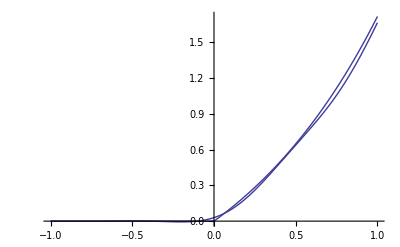
{13.432,-Graphics-}

```mathematica
Timing[Module[{x2=0.1,K=1,λ1=2,λ2=1.1,coeff=LegendreCoeffs[40,-10,10]},g1=ListPlot[Table[{i/100,Re[Module[{x1=i/100},1/(2π)^2 CoeffBasedIntegrate[(ⅇ^(-ⅈ x1( #1+ⅈ λ1)-ⅈ x2( #2-ⅈ λ2))FirstUnderlyingVanillaPayOffFourierGaucheCC[#1+ⅈ λ1,( #2-ⅈ λ2),K,1,1]+ⅇ^(-ⅈ x1( #1+ⅈ λ1)-ⅈ x2( #2+ⅈ λ2))FirstUnderlyingVanillaPayOffFourierDroiteCC[#1+ⅈ λ1,( #2+ⅈ λ2),K,1,1])&,coeff,coeff]]]},{i,-100,100}],Joined->True];
g2=ListPlot[Table[{i/100,Module[{x1=i/100},Re[FirstUnderlyingPayOff[x1,x2,K]]]},{i,-100,100}],Joined->True];
Show[g1,g2,PlotRange->All]]]
```

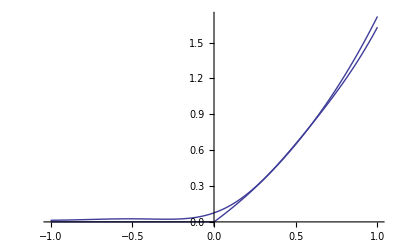
{11.669,-Graphics-}

```mathematica
Timing[Module[{x1=0.1,K=1,λ1=2,λ2=1.2,coeff=RiemanCoeffs[40,-8,8]},g1=ListPlot[Table[{i/100,Re[Module[{x2=i/100},1/(2π)^2 CoeffBasedIntegrate[(ⅇ^(-ⅈ x1( #1-ⅈ λ1)-ⅈ x2( #2+ⅈ λ2))SecondUnderlyingVanillaPayOffFourierGaucheCC[#1-ⅈ λ1,( #2+ⅈ λ2),K,1,1]+ⅇ^(-ⅈ x1( #1+ⅈ λ1)-ⅈ x2( #2+ⅈ λ2))SecondUnderlyingVanillaPayOffFourierDroiteCC[#1+ⅈ λ1,( #2+ⅈ λ2),K,1,1])&,coeff,coeff]]]},{i,-100,100}],Joined->True];
g2=ListPlot[Table[{i/100,Module[{x2=i/100},Re[SecondUnderlyingPayOff[x1,x2,K]]]},{i,-100,100}],Joined->True];
Show[g1,g2,PlotRange->All]]]
```

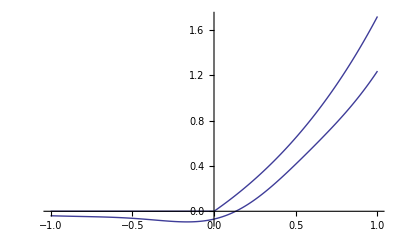
{13.026,-Graphics-}

```mathematica
Timing[Module[{x1=0.1,K=1,λ1=2,λ2=1.2,coeff=LegendreCoeffs[40,-8,8]},g1=ListPlot[Table[{i/100,Re[Module[{x2=i/100},1/(2π)^2 CoeffBasedIntegrate[(ⅇ^(-ⅈ x1( #1-ⅈ λ1)-ⅈ x2( #2+ⅈ λ2))SecondUnderlyingVanillaPayOffFourierGaucheCC[#1-ⅈ λ1,( #2+ⅈ λ2),K,1,1]+ⅇ^(-ⅈ x1( #1+ⅈ λ1)-ⅈ x2( #2+ⅈ λ2))SecondUnderlyingVanillaPayOffFourierDroiteCC[#1+ⅈ λ1,( #2+ⅈ λ2),K,1,1])&,coeff,coeff]]]},{i,-100,100}],Joined->True];
g2=ListPlot[Table[{i/100,Module[{x2=i/100},Re[SecondUnderlyingPayOff[x1,x2,K]]]},{i,-100,100}],Joined->True];
Show[g1,g2,PlotRange->All]]]
```

## Calculs Formel :(α S_1^a-β S_2^b-K)^+

### Calculs Formels x2> 0

```mathematica
Solve[α ⅇ^(a x1)-β ⅇ^(b x2)-K==0,x1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x1→Log[-(-K-ⅇ^(b x2) β)/α]/a}}

```mathematica
integration1=Simplify[∫_(Log[-(-K-ⅇ^(b  x2) β)/α]/a)^∞ ⅇ^(ⅈ  k1 x1)(α ⅇ^(a  x1)-β ⅇ^(b  x2)-K)ⅆx1]
```

If[Im[k1]>0&&Re[a]<Im[k1],-(ⅈ a α ((K+ⅇ^(b x2) β)/α)^(1+(ⅈ k1)/a))/((a+ⅈ k1) k1),Integrate[-ⅇ^(ⅈ k1 x1) K+ⅇ^(a x1+ⅈ k1 x1) α-ⅇ^(ⅈ k1 x1+b x2) β,{x1,Log[-(-K-ⅇ^(b x2) β)/α]/a,∞},Assumptions→(Re[a]≤0&&Im[k1]≤0)||(Re[a]>0&&Im[k1]≤Re[a])]]

```mathematica
integration11=Simplify[integration1,Im[k1]>0&&Re[a]<Im[k1]]
```

-(ⅈ a α ((K+ⅇ^(b x2) β)/α)^(1+(ⅈ k1)/a))/((a+ⅈ k1) k1)

```mathematica
Simplify[Integrate[ⅇ^(ⅈ  k2  x2)integration11,x2],K>0]
```

-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a ⅇ^(ⅈ k2 x2) ((K+ⅇ^(b x2) β)/α)^((ⅈ k1)/a) (1+(ⅇ^(b x2) β)/K)^(-(ⅈ k1)/a) (K (-ⅈ b+k2) Hypergeometric2F1[-(ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,-(ⅇ^(b x2) β)/K]+ⅇ^(b x2) k2 β Hypergeometric2F1[-(ⅈ k1)/a,1+(ⅈ k2)/b,2+(ⅈ k2)/b,-(ⅇ^(b x2) β)/K])

ca converge pour Im[k1] > a,  Im[k2] > 0  pour x2 ∈ [0, +∞[

```mathematica
on fabrique donc F[x2=∞] -F[x2=0] pour obtenir l'integrale (x2>0)
```

```mathematica
finf=-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a ⅇ^(ⅈ k2 x2) (1/α)^((ⅈ k1)/a) (1/K)^(-(ⅈ k1)/a) (K (-ⅈ b+k2) Hypergeometric2F1[-(ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,0]+ⅇ^(b x2) k2 β Hypergeometric2F1[-(ⅈ k1)/a,1+(ⅈ k2)/b,2+(ⅈ k2)/b,0])=0
```

```mathematica
on emploie :
```

```mathematica
RuleHyper={Hypergeometric2F1[a_,b_,c_,z_]->(Gamma[b-a] Gamma[c])/(Gamma[b]Gamma[c-a])(-z)^-a Hypergeometric2F1[a,a-c+1,a-b+1,1/z]+(Gamma[a-b] Gamma[c])/(Gamma[a] Gamma[c-b])(-z)^-b Hypergeometric2F1[b,b-c+1,b-a+1,1/z]};
```

```mathematica
-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a ⅇ^(ⅈ k2 x2) (1/α)^((ⅈ k1)/a) (1/K)^(-(ⅈ k1)/a) (K (-ⅈ b+k2) Hypergeometric2F1[-(ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,-(ⅇ^(b x2) β)/K]+ⅇ^(b x2) k2 β Hypergeometric2F1[-(ⅈ k1)/a,1+(ⅈ k2)/b,2+(ⅈ k2)/b,-(ⅇ^(b x2) β)/K])/.RuleHyper
```

-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a ⅇ^(ⅈ k2 x2) (1/K)^(-(ⅈ k1)/a) (1/α)^((ⅈ k1)/a) (ⅇ^(b x2) k2 β ((((ⅇ^(b x2) β)/K)^(-1-(ⅈ k2)/b) Gamma[-1-(ⅈ k1)/a-(ⅈ k2)/b] Gamma[2+(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a]+(((ⅇ^(b x2) β)/K)^((ⅈ k1)/a) Gamma[2+(ⅈ k2)/b] Gamma[1+(ⅈ k1)/a+(ⅈ k2)/b] Hypergeometric2F1[-(ⅈ k1)/a,-1-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅇ^(-b x2) K)/β])/(Gamma[1+(ⅈ k2)/b] Gamma[2+(ⅈ k1)/a+(ⅈ k2)/b]))+K (-ⅈ b+k2) ((((ⅇ^(b x2) β)/K)^(-(ⅈ k2)/b) Gamma[-(ⅈ k1)/a-(ⅈ k2)/b] Gamma[1+(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a]+(((ⅇ^(b x2) β)/K)^((ⅈ k1)/a) Gamma[1+(ⅈ k2)/b] Gamma[(ⅈ k1)/a+(ⅈ k2)/b] Hypergeometric2F1[-(ⅈ k1)/a,-(ⅈ k1)/a-(ⅈ k2)/b,1-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅇ^(-b x2) K)/β])/(Gamma[(ⅈ k2)/b] Gamma[1+(ⅈ k1)/a+(ⅈ k2)/b])))

```mathematica
la partie hypergeometrique s'annule a l'infini pouvu que Im[k2] > Re[b]
```

```mathematica
-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a ⅇ^(ⅈ k2 x2) (1/K)^(-(ⅈ k1)/a) (1/α)^((ⅈ k1)/a) (ⅇ^(b x2) k2 β ((((ⅇ^(b x2) β)/K)^(-1-(ⅈ k2)/b) Gamma[-1-(ⅈ k1)/a-(ⅈ k2)/b] Gamma[2+(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a])+K (-ⅈ b+k2) ((((ⅇ^(b x2) β)/K)^(-(ⅈ k2)/b) Gamma[-(ⅈ k1)/a-(ⅈ k2)/b] Gamma[1+(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a]))
```

```mathematica
-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a  K^(1+(ⅈ k2)/b+(ⅈ k1)/a) α^(-(ⅈ k1)/a)  β^(-(ⅈ k2)/b)(Gamma[1+(ⅈ k2)/b]Gamma[-1-(ⅈ k1)/a-(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a]( k2 ( (1+(ⅈ k2)/b))+(-ⅈ b+k2) ( (-1-(ⅈ k1)/a-(ⅈ k2)/b) ))
```

```mathematica
Simplify[( k2 ( (1+(ⅈ k2)/b))+(-ⅈ b+k2) ( (-1-(ⅈ k1)/a-(ⅈ k2)/b) ))]
```

(ⅈ (a+ⅈ k1) (b+ⅈ k2))/a

```mathematica
1/(k1 k2)  K^(1+(ⅈ k2)/b+(ⅈ k1)/a) α^(-(ⅈ k1)/a)  β^(-(ⅈ k2)/b)(Gamma[1+(ⅈ k2)/b]Gamma[-1-(ⅈ k1)/a-(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a]
```

```mathematica
or on aussi que
```

```mathematica
f0=-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a  (1/α)^((ⅈ k1)/a) (1/K)^(-(ⅈ k1)/a) (K (-ⅈ b+k2) Hypergeometric2F1[-(ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,-β/K]+ k2 β Hypergeometric2F1[-(ⅈ k1)/a,1+(ⅈ k2)/b,2+(ⅈ k2)/b,-β/K])
```

```mathematica
donc
optplus=1/(k1 k2)  K^(1+(ⅈ k2)/b+(ⅈ k1)/a) α^(-(ⅈ k1)/a)  β^(-(ⅈ k2)/b)(Gamma[1+(ⅈ k2)/b]Gamma[-1-(ⅈ k1)/a-(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a]+1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a  (1/α)^((ⅈ k1)/a) (1/K)^(-(ⅈ k1)/a) (K (-ⅈ b+k2) Hypergeometric2F1[-(ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,-β/K]+ k2 β Hypergeometric2F1[-(ⅈ k1)/a,1+(ⅈ k2)/b,2+(ⅈ k2)/b,-β/K])
```

```mathematica
On applique alors la regle et maintenant il ne reste plus que la partie hypergeometrique !
```

```mathematica
-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a  (1/K)^(-(ⅈ k1)/a) (1/α)^((ⅈ k1)/a) ( k2 β (((β/K)^((ⅈ k1)/a) Gamma[2+(ⅈ k2)/b] Gamma[1+(ⅈ k1)/a+(ⅈ k2)/b] Hypergeometric2F1[-(ⅈ k1)/a,-1-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅇ^(-b x2) K)/β])/(Gamma[1+(ⅈ k2)/b] Gamma[2+(ⅈ k1)/a+(ⅈ k2)/b]))+K (-ⅈ b+k2) (((β/K)^((ⅈ k1)/a) Gamma[1+(ⅈ k2)/b] Gamma[(ⅈ k1)/a+(ⅈ k2)/b] Hypergeometric2F1[-(ⅈ k1)/a,-(ⅈ k1)/a-(ⅈ k2)/b,1-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅇ^(-b x2) K)/β])/(Gamma[(ⅈ k2)/b] Gamma[1+(ⅈ k1)/a+(ⅈ k2)/b])))
```

```mathematica
que on simplifie avec la regle classique : x Gamma[x] == Gamma[x+1]
```

```mathematica
optplus=-(ⅈ a   (β/α)^((ⅈ k1)/a))/((a+ⅈ k1) k1 b) ( β (Hypergeometric2F1[-(ⅈ k1)/a,-1-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅇ^(-b x2) K)/β]/(1+(ⅈ k1)/a+(ⅈ k2)/b))+K  (Hypergeometric2F1[-(ⅈ k1)/a,-(ⅈ k1)/a-(ⅈ k2)/b,1-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅇ^(-b x2) K)/β]/((ⅈ k1)/a+(ⅈ k2)/b)))
```

### Calculs Formels x2< 0

```mathematica
on reprends l'expression de la primitive
```

```mathematica
-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a ⅇ^(ⅈ k2 x2) (1/α)^((ⅈ k1)/a) (1/K)^(-(ⅈ k1)/a) (K (-ⅈ b+k2) Hypergeometric2F1[-(ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,-(ⅇ^(b x2) β)/K]+ⅇ^(b x2) k2 β Hypergeometric2F1[-(ⅈ k1)/a,1+(ⅈ k2)/b,2+(ⅈ k2)/b,-(ⅇ^(b x2) β)/K])
```

```mathematica
quand x2 -> -∞ les hypergeometrique deviennent 1  et tout tends vers 0  . donc
```

```mathematica
optmoins =-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a  (K/α)^((ⅈ k1)/a)  (K (-ⅈ b+k2) Hypergeometric2F1[-(ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,-β/K]+ k2 β Hypergeometric2F1[-(ⅈ k1)/a,1+(ⅈ k2)/b,2+(ⅈ k2)/b,-β/K])
```

```mathematica
Il est malgré tout interressant d'voir les formule valable pour K tres petit
```

```mathematica
-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a  (K/α)^((ⅈ k1)/a)  (K (-ⅈ b+k2) Hypergeometric2F1[-(ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,-β/K]+ k2 β Hypergeometric2F1[-(ⅈ k1)/a,1+(ⅈ k2)/b,2+(ⅈ k2)/b,-β/K]) /.RuleHyper
```

-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a (K/α)^((ⅈ k1)/a) (k2 β (((β/K)^(-1-(ⅈ k2)/b) Gamma[-1-(ⅈ k1)/a-(ⅈ k2)/b] Gamma[2+(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a]+((β/K)^((ⅈ k1)/a) Gamma[2+(ⅈ k2)/b] Gamma[1+(ⅈ k1)/a+(ⅈ k2)/b] Hypergeometric2F1[-(ⅈ k1)/a,-1-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅈ k1)/a-(ⅈ k2)/b,-K/β])/(Gamma[1+(ⅈ k2)/b] Gamma[2+(ⅈ k1)/a+(ⅈ k2)/b]))+K (-ⅈ b+k2) (((β/K)^(-(ⅈ k2)/b) Gamma[-(ⅈ k1)/a-(ⅈ k2)/b] Gamma[1+(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a]+((β/K)^((ⅈ k1)/a) Gamma[1+(ⅈ k2)/b] Gamma[(ⅈ k1)/a+(ⅈ k2)/b] Hypergeometric2F1[-(ⅈ k1)/a,-(ⅈ k1)/a-(ⅈ k2)/b,1-(ⅈ k1)/a-(ⅈ k2)/b,-K/β])/(Gamma[(ⅈ k2)/b] Gamma[1+(ⅈ k1)/a+(ⅈ k2)/b])))

```mathematica
optmoins=-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a (K/α)^((ⅈ k1)/a) (k2 β (((β/K)^(-1-(ⅈ k2)/b) Gamma[-1-(ⅈ k1)/a-(ⅈ k2)/b] Gamma[2+(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a]+((β/K)^((ⅈ k1)/a)(1+(ⅈ k2)/b)  Hypergeometric2F1[-(ⅈ k1)/a,-1-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅈ k1)/a-(ⅈ k2)/b,-K/β])/(1+(ⅈ k1)/a+(ⅈ k2)/b))+K (-ⅈ b+k2) (((β/K)^(-(ⅈ k2)/b) Gamma[-(ⅈ k1)/a-(ⅈ k2)/b] Gamma[1+(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a]+((β/K)^((ⅈ k1)/a) ((ⅈ k2)/b) Hypergeometric2F1[-(ⅈ k1)/a,-(ⅈ k1)/a-(ⅈ k2)/b,1-(ⅈ k1)/a-(ⅈ k2)/b,-K/β])/((ⅈ k1)/a+(ⅈ k2)/b)))
```

```mathematica
VanillaPayOffFourierGauche[k1_,k2_,K_,α_,β_,a_,b_]:=Module[{H=(Gamma[-1-(ⅈ k1)/a-(ⅈ k2)/b] Gamma[1+(ⅈ k2)/b])/Gamma[-(ⅈ k1)/a],g1=(β/K)^(-(ⅈ k2)/b),g2=(β/K)^((ⅈ k1)/a)},
-1/((a+ⅈ k1) k1 k2 (-ⅈ b+k2))a (K/α)^((ⅈ k1)/a) (k2 β (K/β g1 H(1+(ⅈ k2)/b)+(g2(1+(ⅈ k2)/b)  Hypergeometric2F1[-(ⅈ k1)/a,-1-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅈ k1)/a-(ⅈ k2)/b,-K/β])/(1+(ⅈ k1)/a+(ⅈ k2)/b))+
K (-ⅈ b+k2) (g1  H(-1-(ⅈ k1)/a-(ⅈ k2)/b) +(g2 ((ⅈ k2)/b) Hypergeometric2F1[-(ⅈ k1)/a,-(ⅈ k1)/a-(ⅈ k2)/b,1-(ⅈ k1)/a-(ⅈ k2)/b,-K/β])/((ⅈ k1)/a+(ⅈ k2)/b)))]
```

### Verification de la limite quand k -> 0

```mathematica
Simplify[(-(ⅈ a   (β/α)^((ⅈ k1)/a))/((a+ⅈ k1) k1 b) ( β (Hypergeometric2F1[-(ⅈ k1)/a,-1-(ⅈ k1)/a-(ⅈ k2)/b,-(ⅈ k1)/a-(ⅈ k2)/b,-K/β]/(1+(ⅈ k1)/a+(ⅈ k2)/b))+K  (Hypergeometric2F1[-(ⅈ k1)/a,-(ⅈ k1)/a-(ⅈ k2)/b,1-(ⅈ k1)/a-(ⅈ k2)/b,-K/β]/((ⅈ k1)/a+(ⅈ k2)/b)))) /. K->0,x2>0]
```

(a^2 β (β/α)^((ⅈ k1)/a))/((ⅈ a-k1) k1 (a b+ⅈ b k1+ⅈ a k2))

### Calculs Formels K = 0

```mathematica
Simplify[Solve[α ⅇ^(a x1)-β ⅇ^(b x2)==0,x1],α>0&&β>0&&b>0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x1→Log[(ⅇ^(b x2) β)/α]/a}}

```mathematica
Simplify[Solve[a x1+Log[α]==b x2+Log[β],x1],α>0&&β>0&&b>0]
```

{{x1→(b x2-Log[α]+Log[β])/a}}

```mathematica
=b x2+Log[β/α]/a
```

```mathematica
integration1=Simplify[∫_(b/a x2+Log[β/α]/a)^∞ ⅇ^(ⅈ k1 x1)(α ⅇ^(a x1)-β ⅇ^(b x2))ⅆx1]
```

If[Im[k1]>0&&Re[a]<Im[k1],(a ⅇ^(b x2+(ⅈ b k1 x2)/a) β (β/α)^((ⅈ k1)/a))/(ⅈ a k1-k1^2),Integrate[ⅇ^(a x1+ⅈ k1 x1) α-ⅇ^(ⅈ k1 x1+b x2) β,{x1,(b x2)/a+Log[β/α]/a,∞},Assumptions→(Re[a]≤0&&Im[k1]≤0)||(Re[a]>0&&Im[k1]≤Re[a])]]

```mathematica
integration11=Simplify[integration1,Im[k1]>0&&Re[a]<Im[k1]]
```

(a ⅇ^(b x2+(ⅈ b k1 x2)/a) β (β/α)^((ⅈ k1)/a))/(ⅈ a k1-k1^2)

```mathematica
Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration11,x2],K>0]
```

(a^2 ⅇ^((b+(ⅈ b k1)/a+ⅈ k2) x2) β (β/α)^((ⅈ k1)/a))/((ⅈ a-k1) k1 (a b+ⅈ b k1+ⅈ a k2))

```mathematica
Module[{x2=1.2,a=1.31,b=0.78,α=0.87,β=1.09,k1=4.31,k2=3.158},{(a^2 β (β/α)^((ⅈ k1)/a))/((ⅈ a-k1) k1 (a b+ⅈ b k1+ⅈ a k2)),(a^2  β (β/α)^((ⅈ k1)/a))/((ⅈ a-k1) k1 (a b+ⅈ b k1+ⅈ a k2))}]
```

{-0.0117325+0.00494082 ⅈ,-0.0117325+0.00494082 ⅈ}

## Calculs Formel :(Max[α S_1^a,β S_2^b]-K)^+

```mathematica
=SuperPlus[(e^Max[a Subscript[x, 1]+Log[α],b Subscript[x, 2]+Log[β]]-K)]
```

```mathematica
Solve[a x1+Log[α]==b x2+Log[β],x1]
```

{{x1→(b x2-Log[α]+Log[β])/a}}

```mathematica
Solve[a x1+Log[α]==Log[K],x1]
```

{{x1→(Log[K]-Log[α])/a}}

```mathematica
quand x2<(a x1+Log[α]-Log[β])/b  et  x1>(Log[K]-Log[α])/a on paye   α ⅇ^(a x1+Log[α])-K
```

```mathematica
sinon quand  x1<(b x2-Log[α]+Log[β])/a  et  x2 >(Log[K]-Log[β])/b  on paye β ⅇ^(a x2+Log[β])-K
```

```mathematica
donc le payoff est la somme des deux
```

```mathematica
integration1=Simplify[∫_(-∞)^((a x1+Log[α]-Log[β])/b) ⅇ^(ⅈ k2 x2)(α ⅇ^(a x1+Log[α])-K)ⅆx2]
```

If[Im[k2]<0,(ⅈ ⅇ^((ⅈ k2 (a x1+Log[α]-Log[β]))/b) (K-ⅇ^(a x1) α^2))/k2,Integrate[-ⅇ^(ⅈ k2 x2) K+ⅇ^(a x1+ⅈ k2 x2) α^2,{x2,-∞,(a x1+Log[α]-Log[β])/b},Assumptions→Im[k2]≥0]]

```mathematica
integration11=Simplify[integration1,Im[k2]<0]
```

(ⅈ ⅇ^((ⅈ k2 (a x1+Log[α]-Log[β]))/b) (K-ⅇ^(a x1) α^2))/k2

```mathematica
integration111=Simplify[Integrate[ⅇ^(ⅈ k1 x1)integration11,{x1,(Log[K]-Log[α])/a,∞}],K>0]
```

If[Re[a]<Im[k1]+Im[(a k2)/b]&&Im[k1+(a k2)/b]>0,-(b K^(1+(ⅈ k1)/a+(ⅈ k2)/b) (a (b-ⅈ k2 (-1+α))-ⅈ b k1 (-1+α)) α^(-(ⅈ k1)/a) β^(-(ⅈ k2)/b))/((ⅈ b k1+a (b+ⅈ k2)) k2 (b k1+a k2)),Integrate[(ⅈ ⅇ^(ⅈ (k1 x1+(k2 (a x1+Log[α]-Log[β]))/b)) K)/k2-(ⅈ ⅇ^(a x1+ⅈ (k1 x1+(k2 (a x1+Log[α]-Log[β]))/b)) α^2)/k2,{x1,(Log[K]-Log[α])/a,∞},Assumptions→Im[k1]+Im[(a k2)/b]≤Re[a]||Im[k1+(a k2)/b]≤0]]

```mathematica
Simplify[integration111,Re[a]<Im[k1]+Im[(a k2)/b]&&Im[k1+(a k2)/b]>0]
```

-(b K^(1+(ⅈ k1)/a+(ⅈ k2)/b) (a (b-ⅈ k2 (-1+α))-ⅈ b k1 (-1+α)) α^(-(ⅈ k1)/a) β^(-(ⅈ k2)/b))/((ⅈ b k1+a (b+ⅈ k2)) k2 (b k1+a k2))

```mathematica
donc partie gauche =-(b K^(1+(ⅈ k1)/a+(ⅈ k2)/b) (a (b-ⅈ k2 (-1+α))-ⅈ b k1 (-1+α)) α^(-(ⅈ k1)/a) β^(-(ⅈ k2)/b))/((ⅈ b k1+a (b+ⅈ k2)) k2 (b k1+a k2))   si Re[a]<Im[k1]+Im[(a k2)/b]&&Im[k1+(a k2)/b]>0 && Im[k2]<0
```

```mathematica
de meme
```

```mathematica
integration2=Simplify[∫_(-∞)^((b x2-Log[α]+Log[β])/a) ⅇ^(ⅈ k1  x1)(β ⅇ^(a x2+Log[β])-K)ⅆx1]
```

If[Im[k1]<0,(ⅈ ⅇ^((ⅈ k1 (b x2-Log[α]+Log[β]))/a) (K-ⅇ^(a x2) β^2))/k1,Integrate[-ⅇ^(ⅈ k1 x1) K+ⅇ^(ⅈ k1 x1+a x2) β^2,{x1,-∞,(b x2-Log[α]+Log[β])/a},Assumptions→Im[k1]≥0]]

```mathematica
integration22=Simplify[integration2,Im[k1]<0]
```

(ⅈ ⅇ^((ⅈ k1 (b x2-Log[α]+Log[β]))/a) (K-ⅇ^(a x2) β^2))/k1

```mathematica
integration222=Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration22,{x2,(Log[K]-Log[β])/b,∞}],K>0]
```

If[Re[a]<Im[(b k1)/a]+Im[k2]&&Im[(b k1)/a+k2]>0,(a K^(ⅈ (k1/a+k2/b)) α^(-(ⅈ k1)/a) β^(-(a+ⅈ k2)/b) (ⅈ K^(a/b) (b k1+a k2) β^2-K (a^2+ⅈ b k1+ⅈ a k2) β^(a/b)))/(k1 (a^2+ⅈ b k1+ⅈ a k2) (b k1+a k2)),Integrate[(ⅈ ⅇ^(ⅈ (k2 x2+(k1 (b x2-Log[α]+Log[β]))/a)) K)/k1-(ⅈ ⅇ^(a x2+ⅈ (k2 x2+(k1 (b x2-Log[α]+Log[β]))/a)) β^2)/k1,{x2,(Log[K]-Log[β])/b,∞},Assumptions→Im[(b k1)/a]+Im[k2]≤Re[a]||Im[(b k1)/a+k2]≤0]]

```mathematica
Simplify[integration222,Re[a]<Im[(b k1)/a]+Im[k2]&&Im[(b k1)/a+k2]>0]
```

(a K^(ⅈ (k1/a+k2/b)) α^(-(ⅈ k1)/a) β^(-(a+ⅈ k2)/b) (ⅈ K^(a/b) (b k1+a k2) β^2-K (a^2+ⅈ b k1+ⅈ a k2) β^(a/b)))/(k1 (a^2+ⅈ b k1+ⅈ a k2) (b k1+a k2))

```mathematica
et partie droite =(a K^(ⅈ (k1/a+k2/b)) α^(-(ⅈ k1)/a) β^(-(a+ⅈ k2)/b) (ⅈ K^(a/b) (b k1+a k2) β^2-K (a^2+ⅈ b k1+ⅈ a k2) β^(a/b)))/(k1 (a^2+ⅈ b k1+ⅈ a k2) (b k1+a k2))   si Re[a]<Im[(b k1)/a]+Im[k2]&&Im[(b k1)/a+k2]>0 &&Im[k1]<0
```

```mathematica
Simplify[(a K^(ⅈ (k1/a+k2/b)) α^(-(ⅈ k1)/a) β^(-(a+ⅈ k2)/b) (ⅈ K^(a/b) (b k1+a k2) β^2-K (a^2+ⅈ b k1+ⅈ a k2) β^(a/b)))/(k1 (a^2+ⅈ b k1+ⅈ a k2) (b k1+a k2)) /.{α->1,β->1,a->1,b->1},K>0]
```

(ⅈ K^(ⅈ (-ⅈ+k1+k2)))/(k1 (k1^2+k2 (-ⅈ+k2)+k1 (-ⅈ+2 k2)))

```mathematica
Factor[k1 (k1^2+k2 (-ⅈ+k2)+k1 (-ⅈ+2 k2))]
```

k1 (k1+k2) (-ⅈ+k1+k2)

## Calculs Formel :(S_1^c 1_(α ⅇ^(a x1)-β ⅇ^(b x2)-K>0))^+

```mathematica
Solve[α ⅇ^(a x1)-β ⅇ^(b x2)-K==0,x1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x1→Log[-(-K-ⅇ^(b x2) β)/α]/a}}

```mathematica
integration1=Simplify[∫_(Log[-(-K-ⅇ^(b  x2) β)/α]/a)^∞ ⅇ^(ⅈ  k1 x1) ⅇ^(c  x1)ⅆx1]
```

If[Re[c]<Im[k1],-(((K+ⅇ^(b x2) β)/α)^((c+ⅈ k1)/a))/(c+ⅈ k1),Integrate[ⅇ^((c+ⅈ k1) x1),{x1,Log[-(-K-ⅇ^(b x2) β)/α]/a,∞},Assumptions→Re[c]≥Im[k1]]]

```mathematica
integration11=Simplify[integration1,Re[c]<Im[k1]]
```

-(((K+ⅇ^(b x2) β)/α)^((c+ⅈ k1)/a))/(c+ⅈ k1)

```mathematica
integration111=Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration11,x2],K>0]
```

(ⅈ ⅇ^(ⅈ k2 x2) ((K+ⅇ^(b x2) β)/α)^((c+ⅈ k1)/a) (1+(ⅇ^(b x2) β)/K)^(-(c+ⅈ k1)/a) Hypergeometric2F1[-(c+ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,-(ⅇ^(b x2) β)/K])/((c+ⅈ k1) k2)

```mathematica
Simplify[(ⅈ ⅇ^(ⅈ k2 x2) (K/α)^((c+ⅈ k1)/a)  Hypergeometric2F1[-(c+ⅈ k1)/a,(ⅈ k2)/b,1+(ⅈ k2)/b,-(ⅇ^(b x2) β)/K])/((c+ⅈ k1) k2) /. RuleHyper]
```

(ⅈ ⅇ^(ⅈ k2 x2) (K/α)^((c+ⅈ k1)/a) Gamma[1+(ⅈ k2)/b] ((((ⅇ^(b x2) β)/K)^(-(ⅈ k2)/b) Gamma[-(c+ⅈ k1)/a-(ⅈ k2)/b])/Gamma[-(c+ⅈ k1)/a]+(((ⅇ^(b x2) β)/K)^((c+ⅈ k1)/a) Gamma[(c+ⅈ k1)/a+(ⅈ k2)/b] Hypergeometric2F1[-(c+ⅈ k1)/a,-(c+ⅈ k1)/a-(ⅈ k2)/b,1-(c+ⅈ k1)/a-(ⅈ k2)/b,-(ⅇ^(-b x2) K)/β])/(Gamma[(ⅈ k2)/b] Gamma[1+(c+ⅈ k1)/a+(ⅈ k2)/b])))/((c+ⅈ k1) k2)

```mathematica
(ⅈ  (K/α)^((c+ⅈ k1)/a) Gamma[1+(ⅈ k2)/b] ((( β)^(-(ⅈ k2)/b)(K)^((ⅈ k2)/b) Gamma[-(c+ⅈ k1)/a-(ⅈ k2)/b])/Gamma[-(c+ⅈ k1)/a]+(ⅇ^(((c+ⅈ k1)/a b +ⅈ k2)x2) (β/K)^((c+ⅈ k1)/a) Hypergeometric2F1[-(c+ⅈ k1)/a,-(c+ⅈ k1)/a-(ⅈ k2)/b,1-(c+ⅈ k1)/a-(ⅈ k2)/b,-(ⅇ^(-b x2) K)/β])/(((c+ⅈ k1)/a+(ⅈ k2)/b)Gamma[(ⅈ k2)/b])))/((c+ⅈ k1) k2)
```

```mathematica
la convergence pour le x2>0 est : Re[(c b)/a+ⅈ( (b k1)/a + k2)]<0  soit,b Im[k1]  +a Im[k2]>c b soit  Im[k2]>(c b)/a-b/a Im[k1]
```

```mathematica
la convergence pour le x2<0 est : Re[ⅈ k2]>0 soit,  -Im[k2]>0 soit Im[k2]<0
```

## Calculs Formel :(S_2^c 1_(α ⅇ^(a x1)-β ⅇ^(b x2)-K>0))^+

```mathematica
Solve[α ⅇ^(a x1)-β ⅇ^(b x2)-K==0,x1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x1→Log[-(-K-ⅇ^(b x2) β)/α]/a}}

```mathematica
integration1=Simplify[∫_(Log[-(-K-ⅇ^(b  x2) β)/α]/a)^∞ ⅇ^(ⅈ  k1 x1) ⅇ^(c  x2)ⅆx1]
```

If[Im[k1]>0,(ⅈ ⅇ^(c x2) ((K+ⅇ^(b x2) β)/α)^((ⅈ k1)/a))/k1,Integrate[ⅇ^(ⅈ k1 x1+c x2),{x1,Log[-(-K-ⅇ^(b x2) β)/α]/a,∞},Assumptions→Im[k1]≤0]]

```mathematica
integration11=Simplify[integration1,Im[k1]>0]
```

(ⅈ ⅇ^(c x2) ((K+ⅇ^(b x2) β)/α)^((ⅈ k1)/a))/k1

```mathematica
integration111=Simplify[Integrate[ⅇ^(ⅈ k2 x2)integration11,x2],K>0]
```

(ⅈ ⅇ^((c+ⅈ k2) x2) ((K+ⅇ^(b x2) β)/α)^((ⅈ k1)/a) (1+(ⅇ^(b x2) β)/K)^(-(ⅈ k1)/a) Hypergeometric2F1[-(ⅈ k1)/a,(c+ⅈ k2)/b,(b+c+ⅈ k2)/b,-(ⅇ^(b x2) β)/K])/(k1 (c+ⅈ k2))

```mathematica
Simplify[(ⅈ ⅇ^((c+ⅈ k2) x2) (K/α)^((ⅈ k1)/a)  Hypergeometric2F1[-(ⅈ k1)/a,(c+ⅈ k2)/b,(b+c+ⅈ k2)/b,-(ⅇ^(b x2) β)/K])/(k1 (c+ⅈ k2)) /. RuleHyper]
```

```mathematica
1/(k1 (c+ⅈ k2))ⅈ  (K/α)^((ⅈ k1)/a) Gamma[(b+c+ⅈ k2)/b] (((β/K)^(-(c+ⅈ k2)/b) Gamma[-(ⅈ k1)/a-(c+ⅈ k2)/b])/Gamma[-(ⅈ k1)/a]+(ⅇ^((c+ⅈ k2+(ⅈ b k1)/a) x2)(β/K)^((ⅈ k1)/a) Gamma[(ⅈ k1)/a+(c+ⅈ k2)/b] Hypergeometric2F1[-(ⅈ k1)/a,-(a c+ⅈ b k1+ⅈ a k2)/(a b),1-(ⅈ k1)/a-(c+ⅈ k2)/b,-(ⅇ^(-b x2) K)/β])/(Gamma[1+(ⅈ k1)/a+(c+ⅈ k2)/b] Gamma[(c+ⅈ k2)/b]))
```

```mathematica
la convergence pour le x2>0 est : Re[c+ⅈ k2+(ⅈ b k1)/a]<0 soit, Re[c] -Im[k2+(b k1)/a]<0 soit  c -Im[k2]-b/a Im[ k1 ]<0 soit Im[k2]>c -b/a Im[ k1 ]
```

```mathematica
la convergence pour le x2<0 est : Re[(c+ⅈ k2)]>0 soit, Re[c] -Im[k2]>0 soit Im[k2]<c
```